```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
<<SpinorHelicity6D`
```

===============SpinorHelicity6D================

Authors: Manuel Accettulli Huber (QMUL)

Please report any bug to:

m.accettullihuber@qmul.ac.uk

Version 1.2 , last update 05/06/2020

=============================================

## Primary Amplitudes -> Helicity & Momenta Structures

```mathematica
PrimaryAmplitudeHelicityFields[d_]:= (*This function generates all the possible combination of helicity-charged fields compatible with the dimension of the operator*)
(*Flatten[
Map[
Table[#,{h,#[[2]],IntegerPart[1/2*#[[1]]+#[[2]]]}]&,*)
Flatten[
Table[
If[(2*i+3/2*j)≤ d,{i,j(*,h*)},Nothing], (*The condition for the field number is 2*#gluons + 3/2*#fermions ≤ dimension of the operator*)
{i,0,IntegerPart[d/2]},{j,0,IntegerPart[2*d/3],2}],
1]
(*],
1]*)
```

```mathematica
Column[PrimaryAmplitudeHelicityFields[7]]
```

{0,0}
{0,2}
{0,4}
{1,0}
{1,2}
{2,0}
{2,2}
{3,0}

```mathematica
PrimaryAmplitudeHelicity[d_]:= (*A more refined version of the previous function which distinguishes between helicity configurations*)
Flatten[
Table[
If[((3/2*(fermM+fermP)+2*(gluonsM+gluonsP))≤ d)&&(gluonsM+1/2*fermM≥gluonsP+1/2*fermP), (*The second condition is the restiction to the configurations for which the total helicity is non-positive*)
{{gluonsM,gluonsP},{fermM,fermP}},
Nothing],
{gluonsM,0,IntegerPart[d/2]},{gluonsP,0,IntegerPart[d/2]},{fermM,0,IntegerPart[2*d/3]},{fermP,0,IntegerPart[2*d/3]}],
3]
```

```mathematica
Column[PrimaryAmplitudeHelicity[6]]
```

{{0,0},{0,0}}
{{0,0},{1,0}}
{{0,0},{1,1}}
{{0,0},{2,0}}
{{0,0},{2,1}}
{{0,0},{2,2}}
{{0,0},{3,0}}
{{0,0},{3,1}}
{{0,0},{4,0}}
{{0,1},{2,0}}
{{1,0},{0,0}}
{{1,0},{0,1}}
{{1,0},{0,2}}
{{1,0},{1,0}}
{{1,0},{1,1}}
{{1,0},{2,0}}
{{1,1},{0,0}}
{{1,1},{1,0}}
{{2,0},{0,0}}
{{2,0},{0,1}}
{{2,0},{1,0}}
{{2,1},{0,0}}
{{3,0},{0,0}}

```mathematica
AmplitudesStructure[d_]:= (*This function assign all the compatible derivative number of the operator to the previously generated helicity configurations*)
Flatten[
Map[
Table[
If[(EvenQ[der+#[[2,1]]])&& (*The first four conditions come from the representation theory and they check wheter is possible to form a Lorentz singlet*)
(EvenQ[der+#[[2,2]]])&&
(#[[1,1]]≠1||((#[[2,1]]+der )≥1))&&
(#[[1,2]]≠1||((#[[2,2]]+der )≥1))&&
(der<d-1)&&(*The operator has to have at least two fields in it*)(*&&
(#[[2,1]]≠1||#[[2,2]]≠1||(#[[1,1]]+#[[1,2]]+der≠d-3))*)(*Dirac equation of motion*)
((d-#[[1,1]]-#[[1,2]]-1/2*#[[2,1]]-1/2*#[[2,2]]-der)>3||der==0)(*three- and two- point minimal form factor do not contribute due to three-point kinematics and IBP+on-shellness respectively*),
Append[#,der],
Nothing],
{der,0,IntegerPart[d-2*(#[[1,1]]+#[[1,2]])-3/2*(#[[2,1]]+#[[2,2]])]}]&,
PrimaryAmplitudeHelicity[d]],
1]
```

```mathematica
Column[AmplitudesStructure[8]]
```

{{0,0},{0,0},0}
{{0,0},{0,0},2}
{{0,0},{0,0},4}
{{0,0},{1,1},1}
{{0,0},{1,1},3}
{{0,0},{2,0},0}
{{0,0},{2,0},2}
{{0,0},{2,2},0}
{{0,0},{2,2},2}
{{0,0},{3,1},1}
{{0,0},{4,0},0}
{{0,0},{4,0},2}
{{0,1},{2,0},2}
{{1,0},{0,0},2}
{{1,0},{0,2},2}
{{1,0},{1,1},1}
{{1,0},{2,0},0}
{{1,0},{2,0},2}
{{1,0},{2,2},0}
{{1,0},{4,0},0}
{{1,1},{0,0},2}
{{1,1},{1,1},1}
{{2,0},{0,0},0}
{{2,0},{0,0},2}
{{2,0},{0,2},0}
{{2,0},{1,1},1}
{{2,0},{2,0},0}
{{2,2},{0,0},0}
{{3,0},{0,0},0}
{{4,0},{0,0},0}

```mathematica
AmplitudesScalars[d_]:=
Module[{structures=AmplitudesStructure[d]},
For[i=1,i≤Length[structures],i++,
structures[[i,3]]=d-2*(structures[[i,1,1]]+structures[[i,1,2]])-3/2*(structures[[i,2,1]]+structures[[i,2,2]])-structures[[i,3]]
];
Return[structures];
]
```

```mathematica
Print[MatrixForm[{AmplitudesStructure[8],AmplitudesScalars[8]}]]
```

(({0,0}
{0,0}
0) | ({0,0}
{0,0}
2) | ({0,0}
{0,0}
4) | ({0,0}
{1,1}
1) | ({0,0}
{1,1}
3) | ({0,0}
{2,0}
0) | ({0,0}
{2,0}
2) | ({0,0}
{2,2}
0) | ({0,0}
{2,2}
2) | ({0,0}
{3,1}
1) | ({0,0}
{4,0}
0) | ({0,0}
{4,0}
2) | ({0,1}
{2,0}
2) | ({1,0}
{0,0}
2) | ({1,0}
{0,2}
2) | ({1,0}
{1,1}
1) | ({1,0}
{2,0}
0) | ({1,0}
{2,0}
2) | ({1,0}
{2,2}
0) | ({1,0}
{4,0}
0) | ({1,1}
{0,0}
2) | ({1,1}
{1,1}
1) | ({2,0}
{0,0}
0) | ({2,0}
{0,0}
2) | ({2,0}
{0,2}
0) | ({2,0}
{1,1}
1) | ({2,0}
{2,0}
0) | ({2,2}
{0,0}
0) | ({3,0}
{0,0}
0) | ({4,0}
{0,0}
0)
({0,0}
{0,0}
8) | ({0,0}
{0,0}
6) | ({0,0}
{0,0}
4) | ({0,0}
{1,1}
4) | ({0,0}
{1,1}
2) | ({0,0}
{2,0}
5) | ({0,0}
{2,0}
3) | ({0,0}
{2,2}
2) | ({0,0}
{2,2}
0) | ({0,0}
{3,1}
1) | ({0,0}
{4,0}
2) | ({0,0}
{4,0}
0) | ({0,1}
{2,0}
1) | ({1,0}
{0,0}
4) | ({1,0}
{0,2}
1) | ({1,0}
{1,1}
2) | ({1,0}
{2,0}
3) | ({1,0}
{2,0}
1) | ({1,0}
{2,2}
0) | ({1,0}
{4,0}
0) | ({1,1}
{0,0}
2) | ({1,1}
{1,1}
0) | ({2,0}
{0,0}
4) | ({2,0}
{0,0}
2) | ({2,0}
{0,2}
1) | ({2,0}
{1,1}
0) | ({2,0}
{2,0}
1) | ({2,2}
{0,0}
0) | ({3,0}
{0,0}
2) | ({4,0}
{0,0}
0))

```mathematica
HelicityStructure[d_][{{gluonsM_,gluonsP_},{fermM_,fermP_},ders_}]:=
Module[{angles,squares},

angles=
Flatten[
Join[
Table[{i,i},{i,1,gluonsM}], (*couples of gluon labels for the helicity structure*)
Table[{j},{j,gluonsM+gluonsP+1,gluonsM+gluonsP+fermM}] (*single fermion label for each fermion*)
],
2];

squares=
Flatten[
Join[
Table[{i,i},{i,gluonsM+1,gluonsM+gluonsP}],
Table[{j},{j,gluonsM+gluonsP+fermM+1,gluonsM+gluonsP+fermM+fermP}]
],
2];

Return[{angles,squares}];

]
```

```mathematica
HelicityStructure[30][{{1,2},{8,4},6}]
```

{{1,1,4,5,6,7,8,9,10,11},{2,2,3,3,12,13,14,15}}

```mathematica
(*We want to avoid the repetition of certain operators under permutations of the labels of identical fields: taking the corresponding partition of the integer number of total number of derivatives for a certain number of field (gluonsM, gluonsP, fermM ecc.), we identify each independent operator with the partition of the number of derivates associated to a given particle species.*)
```

```mathematica
IndependentMomenta[gluonsM_,gluonsP_,fermM_,fermP_,scals_,ders_]:=
Module[{moms},
moms=
Module[{fields={gluonsM,gluonsP,fermM,fermP,scals},totalfields},
totalfields=Sum[fields[[n]],{n,1,Length[fields]}];
Table[
Table[
If[(totalfields>3)&&(i==totalfields),Nothing,i],(*The last field can be excluded using MOMENTUM CONSERVATION, if it can be applied (n>3)*)
{i,
Sum[fields[[n]],{n,1,j-1}] (*the fields are labelled in order (all gluonsM) -> (all gluonsP) -> (all fermsM) -> (all fermP) -> (scals)*)
+1,
Sum[fields[[n]],{n,1,j-1}]
+If[fields[[j]]≤ders,fields[[j]],ders] (*For a given species, we can restrict to a number of fields which is less than the total number of derivatives, taking into account the permutations of the labels*)
}
],
{j,1,Length[fields]}
]
];
moms=DeleteCases[moms,{}]; (*delete void lists, because in the following functions the species of the fields are not relevant and we can forget about those that are not contributing*)
Return[moms];
]
```

```mathematica
(*IndependentMomenta[gluonsM_,gluonsP_,fermM_,fermP_,scals_,ders_]:=
Module[{moms},
moms=
Module[{fields={gluonsM,gluonsP,fermM,fermP,scals},totalfields},
totalfields=Sum[fields[[n]],{n,1,Length[fields]}];
Table[
Table[
If[(totalfields>3)&&(i==totalfields),Nothing,i],(*The last field can be excluded using MOMENTUM CONSERVATION, if it can be applied (n>3)*)
{i,
Sum[fields[[n]],{n,1,j-1}] (*the fields are labelled in order (all gluonsM) -> (all gluonsP) -> (all fermsM) -> (all fermP) -> (scals)*)
+1,
Sum[fields[[n]],{n,1,j-1}]
+fields[[j]] (*I will take into account the permutations at the end, while dealing with species and flavours*)
}
],
{j,1,Length[fields]}
]
];
moms=DeleteCases[moms,{}]; (*delete void lists, because in the following functions the species of the fields are not relevant and we can forget about those that are not contributing*)
Return[moms];
]*)
```

```mathematica
IndependentMomenta[1,2,8,4,0,6]
```

{{1},{2,3},{4,5,6,7,8,9},{12,13,14}}

```mathematica
PartitionMomenta[moms_,partition_]:= (*Given a certain partition and a list of momenta of certain fields (e.g. helicity minus gluons), this function repeat and order the momenta according to the partition*)
If[ListQ[partition], (*in the following function, this function will encounter some zeros, instead of a list associated to a partition. In this case it gives Nothing*)
Flatten[
Table[
moms[[i]],
{i,1,Length[partition]},
{j,1,partition[[i]]} (*repeat the corresponding object as many times as it says the element of the partition*)
] (*do it for all the elements of the partition*)
],
Return[Nothing]
]
PartitionMomenta[{1,2,3,4},{3,1}]
PartitionMomenta[{1,2,3,4},{2,1,1,1}]
PartitionMomenta[{1,2,3,4},{2,1,1,1,1}](*The last one gives an error, because the partition is longer than the total number of field (which lenght is given by the total number of derivatives)*)
```

{1,1,1,2}

{1,1,2,3,4}

Part::partw: Part 5 of {1,2,3,4} does not exist.

{1,1,2,3,4,{1,2,3,4}⟦5⟧}

```mathematica
AllPartitions[moms_,ders_]:= (*gives all the permutation of partitions of partitions, given a certain NUMBER of field species contribution to the operator (up to momentum conservation) and number of total derivatives*)
Module[{lengthmoms=Length[moms],partitions},
partitions=
Map[
IntegerPartitions[#]&,
IntegerPartitions[ders,lengthmoms],
{2}
] (*generates partitions of the partitions of the total number of momenta into the number of momenta of the fields*);
partitions=
Flatten[
Map[
Permutations,
Map[
PadRight[#,lengthmoms]&,
Flatten[Tuples/@partitions,1]  (*combine the generated partitions of partitions in such a way that we have a list of list which sum of single elements = number of total derivatives.*)
](*PadRight add zeros such that the number of level 1 elemets of the list is equal to the number of fields in the operator*)
],
1
];
Return[partitions];
]
```

```mathematica
Map[
IntegerPartitions[#]&,
IntegerPartitions[4,3],
{2}
]
```

{{{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}},{{{3},{2,1},{1,1,1}},{{1}}},{{{2},{1,1}},{{2},{1,1}}},{{{2},{1,1}},{{1}},{{1}}}}

```mathematica
Flatten[Tuples/@%,1]
```

{{{4}},{{3,1}},{{2,2}},{{2,1,1}},{{1,1,1,1}},{{3},{1}},{{2,1},{1}},{{1,1,1},{1}},{{2},{2}},{{2},{1,1}},{{1,1},{2}},{{1,1},{1,1}},{{2},{1},{1}},{{1,1},{1},{1}}}

```mathematica
AllPartitions[IndependentMomenta[1,2,2,5,0,3],3]
```

{{{3},0,0,0},{0,{3},0,0},{0,0,{3},0},{0,0,0,{3}},{{2,1},0,0,0},{0,{2,1},0,0},{0,0,{2,1},0},{0,0,0,{2,1}},{{1,1,1},0,0,0},{0,{1,1,1},0,0},{0,0,{1,1,1},0},{0,0,0,{1,1,1}},{{2},{1},0,0},{{2},0,{1},0},{{2},0,0,{1}},{{1},{2},0,0},{{1},0,{2},0},{{1},0,0,{2}},{0,{2},{1},0},{0,{2},0,{1}},{0,{1},{2},0},{0,{1},0,{2}},{0,0,{2},{1}},{0,0,{1},{2}},{{1,1},{1},0,0},{{1,1},0,{1},0},{{1,1},0,0,{1}},{{1},{1,1},0,0},{{1},0,{1,1},0},{{1},0,0,{1,1}},{0,{1,1},{1},0},{0,{1,1},0,{1}},{0,{1},{1,1},0},{0,{1},0,{1,1}},{0,0,{1,1},{1}},{0,0,{1},{1,1}},{{1},{1},{1},0},{{1},{1},0,{1}},{{1},0,{1},{1}},{0,{1},{1},{1}}}

```mathematica
AllMomentaPartition[moms_,partition_]:= (*given a partition of partition, this function assigns it to list of momenta grouped according to the field species*)
Module[{table,lengthmoms=Length[moms]},
If[
Sum[
Boole[Length[partition[[n]]]≤Length[moms[[n]]]],{n,1,lengthmoms}
]==lengthmoms,(*check whether the lenght of the partition of partition is compatible to the length of lists of momenta. An example is shown in the first example below.*)
(table=
Table[
PartitionMomenta[moms[[i]],partition[[i]]],
{i,1,lengthmoms}
];
Return[table]), (*assign to each list of momenta its partition*)
Return[Nothing];
]
]
```

```mathematica
AllMomentaPartition[IndependentMomenta[1,2,2,5,0,3],{{1,1,1},0,0,0}]
```

Nothing

```mathematica
AllMomentaPartition[IndependentMomenta[1,2,2,5,0,3],{0,{1,1},{1},0}]
```

{{2,3},{4}}

```mathematica
MomentaSelection[d_][{{gluonsM_,gluonsP_},{fermM_,fermP_},ders_}]:= (*generates all the independent momenta, their corresponding partitions of partitions and assign all of them to the lists of momenta*)
Module[{scals=d-2(gluonsM+gluonsP)-3/2*(fermM+fermP)-ders,moms},
moms=IndependentMomenta[gluonsM,gluonsP,fermM,fermP,scals,ders];
moms=
Sort[ (* sort the elements according to a canonical order *)
Map[
Flatten,
AllMomentaPartition[moms,#]&/@AllPartitions[moms,ders]
]
];
Return[moms];
]
```

```mathematica
SpinorStructure[d_][{{gluonsM_,gluonsP_},{fermM_,fermP_},ders_}]:= (*appends the list of momenta to both the angles and the squares bracket lists*)
Module[{helicity,momentas,spinors},
helicity=HelicityStructure[d][{{gluonsM,gluonsP},{fermM,fermP},ders}];
momentas=MomentaSelection[d][{{gluonsM,gluonsP},{fermM,fermP},ders}];
spinors=
Table[
Join[momentas[[n]],#]&/@helicity,
{n,1,Length[momentas]}
];
spinors=
Map[
Sort[#]&,
spinors,
{2}
];
Return[spinors];
]
```

```mathematica
MomentaSelection[8][{{0,0},{0,0},4}]
```

{{1,1,1,1},{1,1,1,2},{1,1,2,2},{1,1,2,3}}

```mathematica
HelicityStructure[8][{{0,1},{2,0},2}]
```

{{2,3},{1,1}}

```mathematica
MomentaSelection[8][{{0,1},{2,0},2}]
```

{{1,1},{1,2},{2,2},{2,3}}

```mathematica
SpinorStructure[8][{{0,1},{2,0},2}]
```

{{{1,1,2,3},{1,1,1,1}},{{1,2,2,3},{1,1,1,2}},{{2,2,2,3},{1,1,2,2}},{{2,2,3,3},{1,1,2,3}}}

```mathematica
IndependentMomenta[1,2,8,4,2,4]
```

{{1},{2,3},{4,5,6,7},{12,13,14,15},{16}}

```mathematica
MomentaSelection[30][{{1,2},{8,4},4}]
```

{{1,1,1,1},{1,1,1,2},{1,1,1,4},{1,1,1,12},{1,1,1,16},{1,1,2,2},{1,1,2,3},{1,1,2,3},{1,1,2,4},{1,1,2,12},{1,1,2,16},{1,1,4,4},{1,1,4,5},{1,1,4,5},{1,1,4,12},{1,1,4,16},{1,1,12,12},{1,1,12,13},{1,1,12,13},{1,1,12,16},{1,1,16,16},{1,2,2,2},{1,2,2,3},{1,2,2,4},{1,2,2,12},{1,2,2,16},{1,2,3,4},{1,2,3,12},{1,2,3,16},{1,2,4,4},{1,2,4,5},{1,2,4,12},{1,2,4,16},{1,2,12,12},{1,2,12,13},{1,2,12,16},{1,2,16,16},{1,4,4,4},{1,4,4,5},{1,4,4,12},{1,4,4,16},{1,4,5,6},{1,4,5,12},{1,4,5,16},{1,4,12,12},{1,4,12,13},{1,4,12,16},{1,4,16,16},{1,12,12,12},{1,12,12,13},{1,12,12,16},{1,12,13,14},{1,12,13,16},{1,12,16,16},{1,16,16,16},{2,2,2,2},{2,2,2,3},{2,2,2,4},{2,2,2,12},{2,2,2,16},{2,2,3,3},{2,2,3,4},{2,2,3,12},{2,2,3,16},{2,2,4,4},{2,2,4,5},{2,2,4,5},{2,2,4,12},{2,2,4,16},{2,2,12,12},{2,2,12,13},{2,2,12,13},{2,2,12,16},{2,2,16,16},{2,3,4,4},{2,3,4,4},{2,3,4,5},{2,3,4,12},{2,3,4,16},{2,3,12,12},{2,3,12,12},{2,3,12,13},{2,3,12,16},{2,3,16,16},{2,3,16,16},{2,4,4,4},{2,4,4,5},{2,4,4,12},{2,4,4,16},{2,4,5,6},{2,4,5,12},{2,4,5,16},{2,4,12,12},{2,4,12,13},{2,4,12,16},{2,4,16,16},{2,12,12,12},{2,12,12,13},{2,12,12,16},{2,12,13,14},{2,12,13,16},{2,12,16,16},{2,16,16,16},{4,4,4,4},{4,4,4,5},{4,4,4,12},{4,4,4,16},{4,4,5,5},{4,4,5,6},{4,4,5,12},{4,4,5,16},{4,4,12,12},{4,4,12,13},{4,4,12,13},{4,4,12,16},{4,4,16,16},{4,5,6,7},{4,5,6,12},{4,5,6,16},{4,5,12,12},{4,5,12,12},{4,5,12,13},{4,5,12,16},{4,5,16,16},{4,5,16,16},{4,12,12,12},{4,12,12,13},{4,12,12,16},{4,12,13,14},{4,12,13,16},{4,12,16,16},{4,16,16,16},{12,12,12,12},{12,12,12,13},{12,12,12,16},{12,12,13,13},{12,12,13,14},{12,12,13,16},{12,12,16,16},{12,13,14,15},{12,13,14,16},{12,13,16,16},{12,13,16,16},{12,16,16,16},{16,16,16,16}}

```mathematica
HelicityStructure[30][{{1,2},{8,4},4}]
```

{{1,1,4,5,6,7,8,9,10,11},{2,2,3,3,12,13,14,15}}

```mathematica
CountsToList[list_List]:= (*counts the number of times each distinct element appears and transform the association to a list of lists made of two objects, the label of each element and the counting*)
KeyValueMap[
List,
Counts[list]
]
```

```mathematica
IsSingletDoable[{List1_,List2_}]:= (*the counting of one element can never exceed half of the total number of countings*)
Module[{counts1=Counts[List1],lengthcounts1,counts2=Counts[List2],lengthcounts2,test1,test2},
(*List1 and List2 are made of repeated elements, for example {1,1,1,2,2,3,3,6}*)
lengthcounts1=Length[counts1];
lengthcounts2=Length[counts2];

test1=
Sum[
Boole[
counts1[[i]]≤Length[List1]/2 
],
{i,1,lengthcounts1}
]==lengthcounts1;

test2=
Sum[
Boole[
counts2[[i]]≤Length[List2]/2
],
{i,1,lengthcounts2}
]==lengthcounts2;

If[
test1&&test2,
(Return[
{CountsToList[List1],CountsToList[List2]}
];),
Return[Nothing];
];

]
```

```mathematica
SpinorStructure[6][{{0,0},{0,0},4}]
IsSingletDoable[#]&/@SpinorStructure[6][{{0,0},{0,0},4}]
Column[%]
```

{{{1,1,1,1},{1,1,1,1}},{{1,1,1,2},{1,1,1,2}},{{1,1,2,2},{1,1,2,2}}}

{{{{1,2},{2,2}},{{1,2},{2,2}}}}

{{{1,2},{2,2}},{{1,2},{2,2}}}

```mathematica
SpinorStructure[8][{{0,1},{2,0},2}]
IsSingletDoable[#]&/@SpinorStructure[8][{{0,1},{2,0},2}]
```

{{{1,1,2,3},{1,1,1,1}},{{1,2,2,3},{1,1,1,2}},{{2,2,2,3},{1,1,2,2}},{{2,2,3,3},{1,1,2,3}}}

{{{{2,2},{3,2}},{{1,2},{2,1},{3,1}}}}

```mathematica
AmplitudesStructure[6]
```

{{{0,0},{0,0},0},{{0,0},{0,0},2},{{0,0},{1,1},1},{{0,0},{2,0},0},{{0,0},{2,2},0},{{0,0},{4,0},0},{{1,0},{2,0},0},{{2,0},{0,0},0},{{3,0},{0,0},0}}

```mathematica
AmplitudesScalars[6]
```

{{{0,0},{0,0},6},{{0,0},{0,0},4},{{0,0},{1,1},2},{{0,0},{2,0},3},{{0,0},{2,2},0},{{0,0},{4,0},0},{{1,0},{2,0},1},{{2,0},{0,0},2},{{3,0},{0,0},0}}

```mathematica
Flatten[SpinorStructure[6][#]&/@AmplitudesStructure[6],1];
IsSingletDoable[#]&/@%;
Print[MatrixForm[%]]
```

({} | {}
{{1,1},{2,1}} | {{1,1},{2,1}}
{{1,1},{3,1}} | {{2,1},{3,1}}
{{1,1},{2,1}} | {}
{{1,1},{2,1}} | {{3,1},{4,1}}
{{1,1},{2,1},{3,1},{4,1}} | {}
{{1,2},{2,1},{3,1}} | {}
{{1,2},{2,2}} | {}
{{1,2},{2,2},{3,2}} | {})

```mathematica
PermutationsOfPartitions[counting_,length_]:= (*this function generates the permutations of partitions of a give integer number counting_ into length_ elements (with zeros)*)
If[NonNegative[counting], (*if the counting is negative, the function returns zero*)
Flatten[
Map[
Permutations,
Map[
PadRight[#,length]&, (*PadRight inserts additional zero (if needed) such that the results permutation of a given partition gives length_ elem*)
IntegerPartitions[
counting
]
]
],
1
],
Return[Nothing]
]
```

```mathematica
PermutationsOfPartitions[1,5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
IsLoopLessDoable[lines_List]:= (*given the list of lines coming out from each point, this function tests if a loopless diagram is doable*)
Module[{numberpoints,totalines},

numberpoints=Length[lines];
totalines=Sum[lines[[i]],{i,1,numberpoints}];

If[
(And@@NonNegative[lines])&& (*to make sense, the number of lines cannot be negative*)
(And@@
(LessEqual[#,totalines/2]&/@lines) (*the number of lines coming out of one point cannot be greater than the number of lines coming out of all the remaining points*)
),

Return[lines],

Return[Nothing]
]
]
```

```mathematica
AssignLines[{assignedlines_List,availablelines_List}]:=
Module[{withoutfirst,numberpoints,newavailablelines,newassignedlines,adjacencymatrix,combinations},

If[

Length[availablelines]>2, (*the case with two points is trivial and we deal with it separately*)

(withoutfirst=Drop[availablelines,1]; (*consider the first point and drop it from the initial list*)
numberpoints=Length[availablelines];
newassignedlines=PermutationsOfPartitions[availablelines[[1]],numberpoints-1]; (*the lines of the first point can be assigned to the remaing points in all the possible combinations, given by the permutations of partitions*)

newavailablelines=IsLoopLessDoable[withoutfirst-#]&/@newassignedlines; (*not all the combinations are allowed*)
(*these are the remaining lines per point*)
combinations=Length[newavailablelines];

newassignedlines=(withoutfirst-#)&/@newavailablelines;
newassignedlines=Table[Join[assignedlines,{newassignedlines[[i]]}],{i,1,combinations}]; (*append the combination in which the lines have been distributed to the list of combinations at higher points*)

adjacencymatrix=Table[{newassignedlines[[i]],newavailablelines[[i]]},{i,1,combinations}]; (*all the rows of the adjacency matrices*)
Return[adjacencymatrix];),

If[

availablelines[[1]]==availablelines[[2]],(*if the number of lines from two points are different, the graph is not possible*)

(adjacencymatrix={Join[assignedlines,{{availablelines[[1]]}}]};
Return[adjacencymatrix];),

Return[Nothing];

]
]
]
```

```mathematica
AllGraphs[lines_List]:=
Module[{length=Length[lines],adjacencymatrix},

adjacencymatrix=AssignLines[{{},lines}];

For[i=1,i≤length-2,i++,
adjacencymatrix=Flatten[AssignLines/@adjacencymatrix,1];
]; (*repeat the procedure above until all the lines coming out all the points are assigned*)

Return[adjacencymatrix];
]
```

```mathematica
AllGraphs[{1,1,1,1,1,1}]
```

{{{1,0,0,0,0},{0,0,0,0},{1,0,0},{0,0},{1}},{{1,0,0,0,0},{0,0,0,0},{0,1,0},{0,1},{0}},{{1,0,0,0,0},{0,0,0,0},{0,0,1},{1,0},{0}},{{0,1,0,0,0},{0,1,0,0},{0,0,0},{0,0},{1}},{{0,1,0,0,0},{0,0,1,0},{0,0,0},{0,1},{0}},{{0,1,0,0,0},{0,0,0,1},{0,0,0},{1,0},{0}},{{0,0,1,0,0},{1,0,0,0},{0,0,0},{0,0},{1}},{{0,0,1,0,0},{0,0,1,0},{0,0,1},{0,0},{0}},{{0,0,1,0,0},{0,0,0,1},{0,1,0},{0,0},{0}},{{0,0,0,1,0},{1,0,0,0},{0,0,0},{0,1},{0}},{{0,0,0,1,0},{0,1,0,0},{0,0,1},{0,0},{0}},{{0,0,0,1,0},{0,0,0,1},{1,0,0},{0,0},{0}},{{0,0,0,0,1},{1,0,0,0},{0,0,0},{1,0},{0}},{{0,0,0,0,1},{0,1,0,0},{0,1,0},{0,0},{0}},{{0,0,0,0,1},{0,0,1,0},{1,0,0},{0,0},{0}}}

```mathematica
AllGraphs[{1,1,1,1}]
```

{{{1,0,0},{0,0},{1}},{{0,1,0},{0,1},{0}},{{0,0,1},{1,0},{0}}}

```mathematica
AllGraphs[{3,3,1,2,1}]
```

{{{3,0,0,0},{0,0,0},{1,0},{1}},{{2,1,0,0},{0,1,0},{0,0},{1}},{{2,0,1,0},{1,0,0},{0,0},{1}},{{2,0,1,0},{0,1,0},{0,1},{0}},{{2,0,1,0},{0,0,1},{1,0},{0}},{{2,0,0,1},{0,1,0},{1,0},{0}},{{1,0,2,0},{1,0,1},{0,0},{0}},{{1,1,1,0},{0,1,1},{0,0},{0}},{{1,1,0,1},{0,2,0},{0,0},{0}},{{1,0,1,1},{1,1,0},{0,0},{0}}}

```mathematica
GraphToMatrix[list_List]:= (*from the graph (the assigned lines), this gives the adjacency matrix*)
Module[{matrix,rows=Length[list]+1,columns=(Length[list[[1]]]+1)},
matrix=Table[
If[j==i,
0,(*no loops, please!*)
If[j>i,
list[[i,j-i]],
list[[j,i-j]] (*we considered so fare the adjacency matrix to be symmetric in this case, because direction (which fixes the overall sign of the diagram) is not needed when we look at the independent combinations*)
]
],
{i,1,rows},
{j,1,columns}
]
]
```

```mathematica
lista={{1,2,3,4},{5,6,7},{8,9},{1}}
```

{{1,2,3,4},{5,6,7},{8,9},{1}}

```mathematica
MatrixForm[GraphToMatrix[lista]]
```

(0 | 1 | 2 | 3 | 4
1 | 0 | 5 | 6 | 7
2 | 5 | 0 | 8 | 9
3 | 6 | 8 | 0 | 1
4 | 7 | 9 | 1 | 0)

```mathematica
MatrixForm/@(GraphToMatrix/@AllGraphs[{3,3,1,2,1}])
```

{(0 | 3 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0),(0 | 2 | 1 | 0 | 0
2 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0),(0 | 2 | 0 | 1 | 0
2 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0),(0 | 2 | 0 | 1 | 0
2 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0),(0 | 2 | 0 | 1 | 0
2 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0),(0 | 2 | 0 | 0 | 1
2 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 2 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0),(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0),(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 2 | 0
1 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)}

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[Pi-2 Pi/n *u],b Sin[Pi-2 Pi/n* u]},{u,1,n}]
```

```mathematica
Graphics[Point[ellipseLayout[5,{1,1}]]];
```

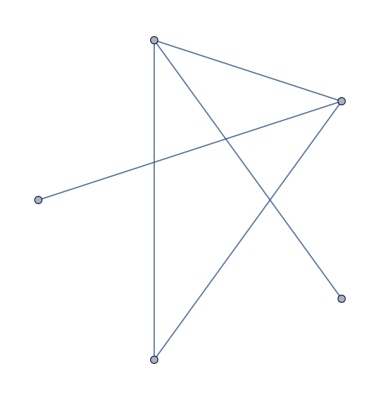
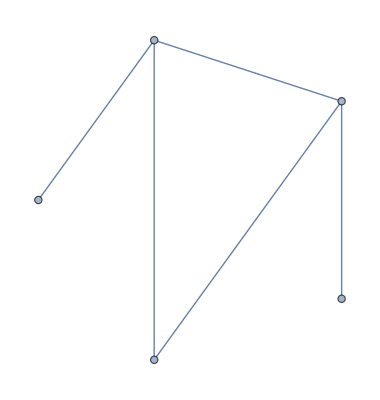
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}]]&/@(GraphToMatrix/@AllGraphs[{3,3,1,2,1}])
```

```mathematica
(*MatrixForm/@*)(GraphToMatrix/@AllGraphs[{1,1,1,1}])
```

{{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

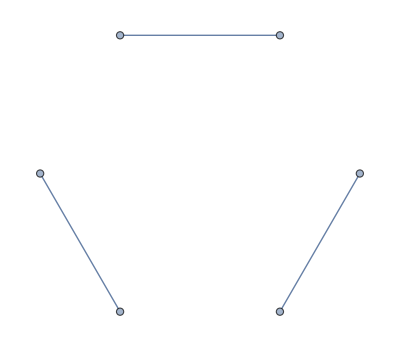
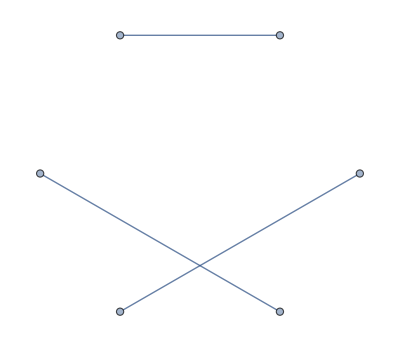
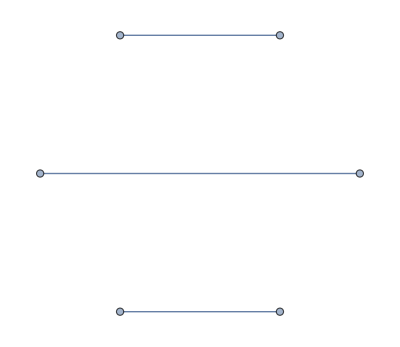
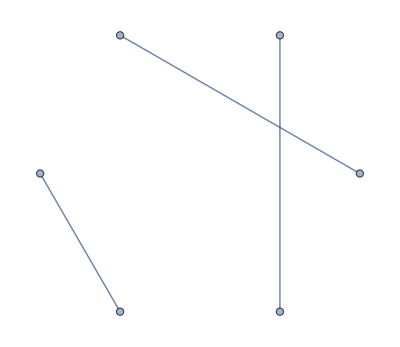
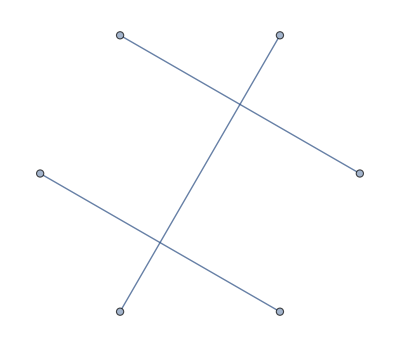
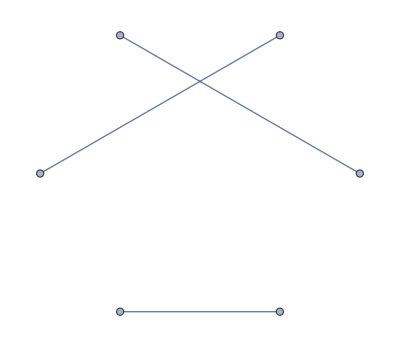
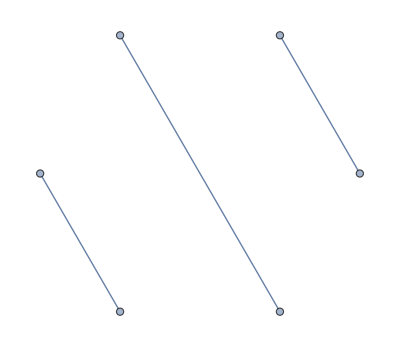
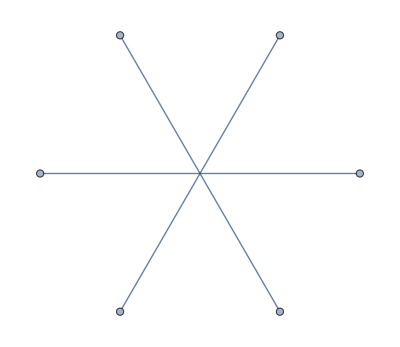

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[6,{1,1}]]&/@(GraphToMatrix/@AllGraphs[{1,1,1,1,1,1}])
```

```mathematica
Options[IsGraphNonIntesercting]={"Intersecting"->False};

IsGraphNonIntesercting[adjacencymatrix_List,OptionsPattern[]]:=
Module[{matrixdim=Length[adjacencymatrix],i,j},
For[i=1,i≤matrixdim,i++,
For[j=i+2,j≤matrixdim-1,j++,
If[
adjacencymatrix[[i,j]]≠0, (*the non-intersection condition translated to the matrix language*)
If[
Sum[adjacencymatrix[[k,l]],{k,i+1,j-1},{l,j+1,matrixdim}]≠0,
If[
OptionValue["Intersecting"],
Return[adjacencymatrix],
Return[Nothing]
];
]
]
]
];
If[
OptionValue["Intersecting"],
Return[Nothing],
Return[adjacencymatrix]
]
]
```

```mathematica
MatrixForm[{{0,2,0,0,0},{2,0,1,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,0,1,0,0}}]
(*AdjacencyGraph[%,VertexCoordinates->ellipseLayout[5,{1,1}]]*)
IsGraphNonIntesercting[%]
```

(0 | 2 | 0 | 0 | 0
2 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

Nothing

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}]]&/@(IsGraphNonIntesercting/@(GraphToMatrix/@AllGraphs[{3,3,1,2,1}]))
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[6,{1,1}]]&/@(IsGraphNonIntesercting/@(GraphToMatrix/@AllGraphs[{1,1,1,1,1,1}]))
(IsGraphNonIntesercting/@(GraphToMatrix/@AllGraphs[{1,1,1,1,1,1}]))
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}},{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,1,0,0,0}},{{0,0,0,1,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}},{{0,0,0,0,0,1},{0,0,1,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}},{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{1,0,0,0,0,0}}}

```mathematica
(*all these graphs can be obtained from permutations of a single graph*)
```

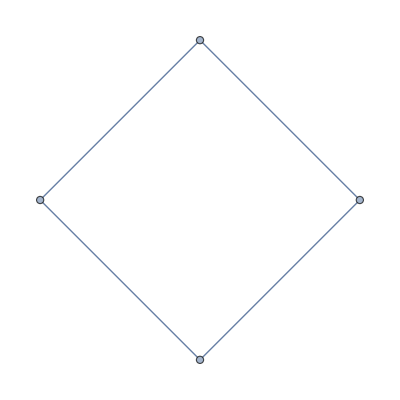
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[4,{1,1}]]&/@(IsGraphNonIntesercting/@(GraphToMatrix/@AllGraphs[{2,2,2,2}]))
```

```mathematica
(*the first two graphs can be obtained by permutations of labels*)
```

```mathematica
AllNonIntersectionGraphs[lines_List]:=
IsGraphNonIntesercting/@(GraphToMatrix/@AllGraphs[lines])
```

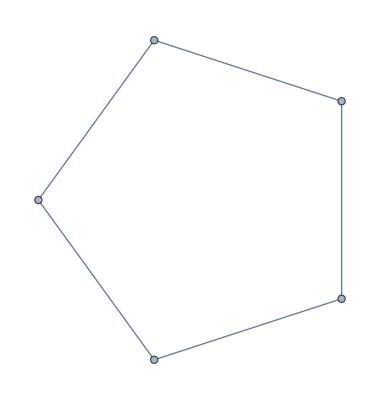
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}]]&/@(GraphToMatrix/@AllGraphs[{2,2,2,2,2}]);
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}]]&/@AllNonIntersectionGraphs[{2,2,2,2,2}]
```

```mathematica
FromMatrixToSpinors[adjacencymatrix_List,labels_List]:=
Module[{numberpoints=Length[labels]},
Product[
Power[
Bracket[labels[[i]],labels[[j]]],
adjacencymatrix[[i,j]] (*gives a bracket to the power indicated by the number of lines between the two corresponding points*)
],
{i,1,numberpoints-1},
{j,i+1,numberpoints}
]
]
```

```mathematica
FromMatrixToSpinors[{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}},{1,2,3,4,7,8}]
```

Bracket[1,2] Bracket[3,4] Bracket[7,8]

```mathematica
FromStructuresToSpinors[pointslines_List]:= (*given the number of labels of the points and the number of lines coming out from each point, this functions generates all the independent bracket structures*)
Module[{labels,lines,numberpoints,graphs,structures},

numberpoints=Length[pointslines];
labels=Table[pointslines[[i,1]],{i,1,numberpoints}];
lines=Table[pointslines[[i,2]],{i,1,numberpoints}];

graphs=AllNonIntersectionGraphs[lines];

structures=FromMatrixToSpinors[#,labels]&/@graphs;
Return[structures];
]
```

```mathematica
FromStructuresToSpinors[{{1,2},{2,1},{3,3},{4,1},{7,4},{9,1}}]/.{Bracket->SpinorAngleBracket}
```

{17^2 23 34 37 79,12 13 37^2 47 79,12 17 34 37^2 79,12 19 37^3 47,13 17 23 37 47 79,17 19 23 37^2 47,17 19 27 34 37^2}

```mathematica
AnglesAndSquares[{anglestructure_List,squarestructure_List}]:=
Module[{formfactors,numberff,angles,squares},

If[anglestructure=={},
angles={1},
angles=ReplaceAll[FromStructuresToSpinors[anglestructure],Bracket->SpinorAngleBracket]
];
If[squarestructure=={},
squares={1},
squares=ReplaceAll[FromStructuresToSpinors[squarestructure],Bracket->SpinorSquareBracket]
];

formfactors=
Times@@@
Tuples[
{angles,squares} (*formfactors so far is a list of {angles,squares}, then Times@@{angles,squares} -> angles * squares. *)
];

Return[formfactors];

]
```

```mathematica
IndependentAnglesAndSquares[{anglestructure_List,squarestructure_List}]:=
Module[{formfactors,numberff,angles,squares},

If[anglestructure=={},
angles={1},
angles=ReplaceAll[FromStructuresToSpinors[anglestructure],Bracket->SpinorAngleBracket]
];
If[squarestructure=={},
squares={1},
squares=ReplaceAll[FromStructuresToSpinors[squarestructure],Bracket->SpinorSquareBracket]
];

Return[{angles,squares}];

]
```

```mathematica
list={{{1,1},{3,2},{4,2},{5,1}},{{2,1},{3,2},{4,2},{5,1}}}
```

{{{1,1},{3,2},{4,2},{5,1}},{{2,1},{3,2},{4,2},{5,1}}}

```mathematica
FromStructuresToSpinors[{{1,1},{3,2},{4,2},{5,1}}]
FromStructuresToSpinors[{{2,1},{3,2},{4,2},{5,1}}]
```

{Bracket[1,3] Bracket[3,4] Bracket[4,5],Bracket[1,5] Bracket[3,4]^2}

{Bracket[2,3] Bracket[3,4] Bracket[4,5],Bracket[2,5] Bracket[3,4]^2}

```mathematica
AnglesAndSquares[list]
```

{13 34 45 23 34 45,13 34 45 25 34^2,15 34^2 23 34 45,15 34^2 25 34^2}

```mathematica
IndependentAnglesAndSquares[list]
```

{{13 34 45,15 34^2},{23 34 45,25 34^2}}

```mathematica
AnglesAndSquares[{{},{}}]
```

{1}

```mathematica
IndependentAnglesAndSquares[{{},{}}]
```

{{1},{1}}

```mathematica
Flatten[SpinorStructure[8][#]&/@AmplitudesStructure[8],1];
IsSingletDoable[#]&/@%;
(*Flatten[AnglesAndSquares[#]&/@%,1];*)
Flatten[AnglesAndSquares[#]&/@%];
operators8=CompleteMandelstam/@%/.{S4->S}
```

{1,S[1,2],S[1,2]^2,S[1,2] S[1,3],13 23,S[1,2] 13 23,S[1,3] 13 23,S[2,3] 13 23,12,S[1,2] 12,S[1,3] 12,S[3,4] 12,14 23 34,12 34,S[1,2] 12 34,12^2 14 23,S[1,3] 12 34,12 13 14,12 34,14 23,S[1,2] 12 34,S[1,2] 14 23,23^2 12 13,12 13 23,12 13 23^2,12^2 23,12 14 34,12 13,S[1,2] 12 13,S[2,3] 12 13,12 13 45,12 13 45,12 15 34,14 15 23,13^2 23^2,13^2 23 24,12^2,S[1,2] 12^2,S[1,3] 12^2,12^2 34,12^2 13 14,12 13 23 34,12^2 34,12 14 23,12^2 34^2,12 13 23,12^2 34^2,14^2 23^2,12 14 23 34}

```mathematica
Flatten[SpinorStructure[6][#]&/@AmplitudesStructure[6],1];
IsSingletDoable[#]&/@%;
(*Flatten[AnglesAndSquares[#]&/@%,1];*)
operator6ind=IndependentAnglesAndSquares[#]&/@%
```

{{{1},{1}},{{12},{12}},{{13},{23}},{{12},{1}},{{12},{34}},{{12 34,14 23},{1}},{{12 13},{1}},{{12^2},{1}},{{12 13 23},{1}}}

```mathematica
Flatten[SpinorStructure[8][#]&/@AmplitudesStructure[8],1];
IsSingletDoable[#]&/@%;
(*Flatten[AnglesAndSquares[#]&/@%,1];*)
operator8ind=IndependentAnglesAndSquares[#]&/@%
```

{{{1},{1}},{{12},{12}},{{12^2},{12^2}},{{12 13},{12 13}},{{13},{23}},{{12 13},{12 23}},{{13^2},{13 23}},{{13 23},{23^2}},{{12},{1}},{{12^2},{12}},{{12 13},{13}},{{12 34,14 23},{34}},{{12},{34}},{{12^2},{12 34,14 23}},{{12 13},{13 34}},{{12 13},{14}},{{12 34,14 23},{1}},{{12^2 34,12 14 23},{12}},{{23^2},{12 13}},{{12 13},{23}},{{12 13},{23^2}},{{12^2},{23}},{{12 14},{34}},{{12 13},{1}},{{12^2 13},{12}},{{12 13 23},{23}},{{12 13},{45}},{{12 13 45,12 15 34,14 15 23},{1}},{{13^2},{23^2}},{{13^2},{23 24}},{{12^2},{1}},{{12^3},{12}},{{12^2 13},{13}},{{12^2},{34}},{{12^2 13},{14}},{{12 13 23},{34}},{{12^2 34,12 14 23},{1}},{{12^2},{34^2}},{{12 13 23},{1}},{{12^2 34^2,14^2 23^2,12 14 23 34},{1}}}

```mathematica
formfactor=12^3 13 23
```

12^3 13 23

```mathematica
HelicityWeight[formfactor]
```

{{1,-2},{2,-2},{3,2}}

```mathematica
MassDimension[formfactor]
```

5

```mathematica
MatterContent[formfactor_,dimO_]:=
Module[{helicities=HelicityWeight[formfactor],numberparticles,dimFF=MassDimension[formfactor],labels={{},{},{},{},{}},numberderivatives,i,numbergluons=0,numberfermions=0,numberscalars=0},
numberparticles=Length[helicities];
For[i=1,i≤numberparticles,i++,
If[helicities[[i,2]]==-2,
(numbergluons++;
labels[[1]]=Append[labels[[1]],helicities[[i,1]]]),
If[helicities[[i,2]]==2,
(numbergluons++;
labels[[2]]=Append[labels[[2]],helicities[[i,1]]]),
If[helicities[[i,2]]==-1,
(numberfermions++;
labels[[3]]=Append[labels[[3]],helicities[[i,1]]]),
If[helicities[[i,2]]==1,
(numberfermions++;
labels[[4]]=Append[labels[[4]],helicities[[i,1]]]),
If[helicities[[i,2]]==0,
(numberscalars++;
labels[[5]]=Append[labels[[5]],helicities[[i,1]]])
]
]
]
]
]
];
For[i=numbergluons+numberfermions+numberscalars+1,i≤(dimO-dimFF),i++,
labels[[5]]=Append[labels[[5]],i];
];
If[labels[[2]]=={},
If[labels[[1]]=={},
numbergluons=0,
numbergluons=Last[labels[[1]]]
],
numbergluons=Last[labels[[2]]]
];
numberderivatives=(dimO-2*numbergluons-3/2*numberfermions-(dimO-dimFF-numbergluons-numberfermions));
Return[{formfactor,labels,numberderivatives}]
]
```

```mathematica
MatterContentStrucutures[formfactorStructures_List,dimO_]:=
Module[{formfactor,helicities,numberparticles,dimFF,labels={{},{},{},{},{}},numberderivatives,i,numbergluons=0,numberfermions=0,numberscalars=0},
formfactor=formfactorStructures[[1,1]]*formfactorStructures[[2,1]];
helicities=HelicityWeight[formfactor];
dimFF=MassDimension[formfactor];
numberparticles=Length[helicities];
For[i=1,i≤numberparticles,i++,
If[helicities[[i,2]]==-2,
(numbergluons++;
labels[[1]]=Append[labels[[1]],helicities[[i,1]]]),
If[helicities[[i,2]]==2,
(numbergluons++;
labels[[2]]=Append[labels[[2]],helicities[[i,1]]]),
If[helicities[[i,2]]==-1,
(numberfermions++;
labels[[3]]=Append[labels[[3]],helicities[[i,1]]]),
If[helicities[[i,2]]==1,
(numberfermions++;
labels[[4]]=Append[labels[[4]],helicities[[i,1]]]),
If[helicities[[i,2]]==0,
(numberscalars++;
labels[[5]]=Append[labels[[5]],helicities[[i,1]]])
]
]
]
]
]
];
For[i=numbergluons+numberfermions+numberscalars+1,i≤(dimO-dimFF),i++,
labels[[5]]=Append[labels[[5]],i];
];
If[labels[[2]]=={},
If[labels[[1]]=={},
numbergluons=0,
numbergluons=Last[labels[[1]]]
],
numbergluons=Last[labels[[2]]]
];
numberderivatives=(dimO-2*numbergluons-3/2*numberfermions-(dimO-dimFF-numbergluons-numberfermions));
Return[{formfactorStructures,labels,numberderivatives}]
]
```

```mathematica
MatterContent[#,8]&/@operators8;
MatrixForm[%]
```

(1 | {{},{},{},{},{1,2,3,4,5,6,7,8}} | 0
S[1,2] | {{},{},{},{},{1,2,3,4,5,6}} | 2
S[1,2]^2 | {{},{},{},{},{1,2,3,4}} | 4
S[1,2] S[1,3] | {{},{},{},{},{1,2,3,4}} | 4
13 23 | {{},{},{1},{2},{3,4,5,6}} | 1
S[1,2] 13 23 | {{},{},{1},{2},{3,4}} | 3
S[1,3] 13 23 | {{},{},{1},{2},{3,4}} | 3
S[2,3] 13 23 | {{},{},{1},{2},{3,4}} | 3
12 | {{},{},{1,2},{},{3,4,5,6,7}} | 0
S[1,2] 12 | {{},{},{1,2},{},{3,4,5}} | 2
S[1,3] 12 | {{},{},{1,2},{},{3,4,5}} | 2
S[3,4] 12 | {{},{},{1,2},{},{3,4,5}} | 2
14 23 34 | {{},{},{1,2},{},{3,4,5}} | 2
12 34 | {{},{},{1,2},{3,4},{5,6}} | 0
S[1,2] 12 34 | {{},{},{1,2},{3,4},{}} | 2
12^2 14 23 | {{},{},{1,2},{3,4},{}} | 2
S[1,3] 12 34 | {{},{},{1,2},{3,4},{}} | 2
12 13 14 | {{},{},{1,2,3},{4},{5}} | 1
12 34 | {{},{},{1,2,3,4},{},{5,6}} | 0
14 23 | {{},{},{1,2,3,4},{},{5,6}} | 0
S[1,2] 12 34 | {{},{},{1,2,3,4},{},{}} | 2
S[1,2] 14 23 | {{},{},{1,2,3,4},{},{}} | 2
23^2 12 13 | {{},{1},{2,3},{},{4}} | 2
12 13 23 | {{1},{},{},{},{2,3,4,5}} | 2
12 13 23^2 | {{1},{},{},{2,3},{4}} | 2
12^2 23 | {{1},{},{2},{3},{4,5}} | 1
12 14 34 | {{1},{},{2},{3},{4,5}} | 1
12 13 | {{1},{},{2,3},{},{4,5,6}} | 0
S[1,2] 12 13 | {{1},{},{2,3},{},{4}} | 2
S[2,3] 12 13 | {{1},{},{2,3},{},{4}} | 2
12 13 45 | {{1},{},{2,3},{4,5},{}} | 0
12 13 45 | {{1},{},{2,3,4,5},{},{}} | 0
12 15 34 | {{1},{},{2,3,4,5},{},{}} | 0
14 15 23 | {{1},{},{2,3,4,5},{},{}} | 0
13^2 23^2 | {{1},{2},{},{},{3,4}} | 2
13^2 23 24 | {{1},{2},{3},{4},{}} | 1
12^2 | {{1,2},{},{},{},{3,4,5,6}} | 0
S[1,2] 12^2 | {{1,2},{},{},{},{3,4}} | 2
S[1,3] 12^2 | {{1,2},{},{},{},{3,4}} | 2
12^2 34 | {{1,2},{},{},{3,4},{5}} | 0
12^2 13 14 | {{1,2},{},{3},{4},{}} | 1
12 13 23 34 | {{1,2},{},{3},{4},{}} | 1
12^2 34 | {{1,2},{},{3,4},{},{5}} | 0
12 14 23 | {{1,2},{},{3,4},{},{5}} | 0
12^2 34^2 | {{1,2},{3,4},{},{},{}} | 0
12 13 23 | {{1,2,3},{},{},{},{4,5}} | 0
12^2 34^2 | {{1,2,3,4},{},{},{},{}} | 0
14^2 23^2 | {{1,2,3,4},{},{},{},{}} | 0
12 14 23 34 | {{1,2,3,4},{},{},{},{}} | 0)

```mathematica
MatterContentStrucutures[#,8]&/@operator8ind;
MatrixForm[%]
```

({{1},{1}} | {{},{},{},{},{1,2,3,4,5,6,7,8}} | 0
{{12},{12}} | {{},{},{},{},{1,2,3,4,5,6}} | 2
{{12^2},{12^2}} | {{},{},{},{},{1,2,3,4}} | 4
{{12 13},{12 13}} | {{},{},{},{},{1,2,3,4}} | 4
{{13},{23}} | {{},{},{1},{2},{3,4,5,6}} | 1
{{12 13},{12 23}} | {{},{},{1},{2},{3,4}} | 3
{{13^2},{13 23}} | {{},{},{1},{2},{3,4}} | 3
{{13 23},{23^2}} | {{},{},{1},{2},{3,4}} | 3
{{12},{1}} | {{},{},{1,2},{},{3,4,5,6,7}} | 0
{{12^2},{12}} | {{},{},{1,2},{},{3,4,5}} | 2
{{12 13},{13}} | {{},{},{1,2},{},{3,4,5}} | 2
{{12 34,14 23},{34}} | {{},{},{1,2},{},{3,4,5}} | 2
{{12},{34}} | {{},{},{1,2},{3,4},{5,6}} | 0
{{12^2},{12 34,14 23}} | {{},{},{1,2},{3,4},{}} | 2
{{12 13},{13 34}} | {{},{},{1,2},{3,4},{}} | 2
{{12 13},{14}} | {{},{},{1,2,3},{4},{5}} | 1
{{12 34,14 23},{1}} | {{},{},{1,2,3,4},{},{5,6}} | 0
{{12^2 34,12 14 23},{12}} | {{},{},{1,2,3,4},{},{}} | 2
{{23^2},{12 13}} | {{},{1},{2,3},{},{4}} | 2
{{12 13},{23}} | {{1},{},{},{},{2,3,4,5}} | 2
{{12 13},{23^2}} | {{1},{},{},{2,3},{4}} | 2
{{12^2},{23}} | {{1},{},{2},{3},{4,5}} | 1
{{12 14},{34}} | {{1},{},{2},{3},{4,5}} | 1
{{12 13},{1}} | {{1},{},{2,3},{},{4,5,6}} | 0
{{12^2 13},{12}} | {{1},{},{2,3},{},{4}} | 2
{{12 13 23},{23}} | {{1},{},{2,3},{},{4}} | 2
{{12 13},{45}} | {{1},{},{2,3},{4,5},{}} | 0
{{12 13 45,12 15 34,14 15 23},{1}} | {{1},{},{2,3,4,5},{},{}} | 0
{{13^2},{23^2}} | {{1},{2},{},{},{3,4}} | 2
{{13^2},{23 24}} | {{1},{2},{3},{4},{}} | 1
{{12^2},{1}} | {{1,2},{},{},{},{3,4,5,6}} | 0
{{12^3},{12}} | {{1,2},{},{},{},{3,4}} | 2
{{12^2 13},{13}} | {{1,2},{},{},{},{3,4}} | 2
{{12^2},{34}} | {{1,2},{},{},{3,4},{5}} | 0
{{12^2 13},{14}} | {{1,2},{},{3},{4},{}} | 1
{{12 13 23},{34}} | {{1,2},{},{3},{4},{}} | 1
{{12^2 34,12 14 23},{1}} | {{1,2},{},{3,4},{},{5}} | 0
{{12^2},{34^2}} | {{1,2},{3,4},{},{},{}} | 0
{{12 13 23},{1}} | {{1,2,3},{},{},{},{4,5}} | 0
{{12^2 34^2,14^2 23^2,12 14 23 34},{1}} | {{1,2,3,4},{},{},{},{}} | 0)

```mathematica
MatterContentStrucutures[#,6]&/@operator6ind;
MatrixForm[%]
```

({{1},{1}} | {{},{},{},{},{1,2,3,4,5,6}} | 0
{{12},{12}} | {{},{},{},{},{1,2,3,4}} | 2
{{13},{23}} | {{},{},{1},{2},{3,4}} | 1
{{12},{1}} | {{},{},{1,2},{},{3,4,5}} | 0
{{12},{34}} | {{},{},{1,2},{3,4},{}} | 0
{{12 34,14 23},{1}} | {{},{},{1,2,3,4},{},{}} | 0
{{12 13},{1}} | {{1},{},{2,3},{},{4}} | 0
{{12^2},{1}} | {{1,2},{},{},{},{3,4}} | 0
{{12 13 23},{1}} | {{1,2,3},{},{},{},{}} | 0)

```mathematica
AngleCount[exp_,label_]:=
Join[
Cases[
{exp},
HoldPattern[SpinorAngleBracket[label,_]|SpinorAngleBracket[_,label]]:>1,
∞
],
Cases[
{exp},
HoldPattern[S[label,_]|S[_,label]]:>1,
∞
]
]//Length;
SquareCount[exp_,label_]:=Join[Cases[{exp},HoldPattern[SpinorSquareBracket[label,_]|SpinorSquareBracket[_,label]]:>1,∞],Cases[{exp},HoldPattern[S[label,_]|S[_,label]]:>1,∞]]//Length;
```

```mathematica
AngleCount[S[1,2]13,1]
SquareCount[S[1,2]13,1]
```

2

1

I want to write a function that can recognise that two different form factors are the same after relabelling, e.g. 12^2 34^2,14^2 23^2.
The relabelling of the momenta has already been taken into account, then there is no need to check whether there could be a repetition for the operators by relabelling the scalars, because there enter in the form factors only through the momenta.

```mathematica
ReLabel[exp_,toberelabelled_,newlabels_]:=ReplaceAll[exp,Join[{s_Power:>s,s_Rational:>s},Thread[Flatten[toberelabelled]->Flatten[newlabels]]]]
```

```mathematica
AreSameFormFactor[{firstff_,secondff_},mattercontent_]:=
Module[{localmatter=DeleteCases[mattercontent,{}],allrelabelling,duplicateQ},
allrelabelling=Tuples[Permutations/@localmatter];
duplicateQ=
MemberQ[
ReLabel[secondff,localmatter,#]&/@allrelabelling,
firstff
];
Return[duplicateQ];
]
```

```mathematica
AreSameFormFactor[{12 13 45,12 13 45},MatterContent[12 13 45,8][[2]]]
```

True

```mathematica
IndependentFormFactors[formfactors_List,mattercontent_]:=
Module[{localff=formfactors,couples,length,stop=True},
While[
stop,
If[Length[localff]==1,Return[localff]]; (*one single form factor cannot be repeated*)
couples=Subsets[localff,{2}]; (*takes couples of form factors*)
length=Length[couples];
Do[
If[
AreSameFormFactor[couples[[i]],mattercontent], (*check if a couple is a repetition*)
localff=DeleteCases[localff,couples[[i,2]]]; (*if yes, delete the second f.f. of the couple*)
Break[], (*and generate new couples*)
If[i==length,stop=False] (*if it checked all the couples, we have a list of *)
],
{i,1,length}
]
];
Return[localff];
]
(*An alternative function could generate all the permutations of the first formfactor and check whether there are repetitions in the others and delete them. Then it generates the permutations of the second (remaining) f.f. and so on. This could be faster because the permutations for one type of operators is generated only once.*)
```

```mathematica
formfactors={12 13 45,12 15 34,14 15 23}
IndependentFormFactors[formfactors,MatterContent[12 13 45,8][[2]]]
```

{12 13 45,12 15 34,14 15 23}

{12 13 45}

```mathematica
Subsets[{a,b,c},{2}]
```

{{a,b},{a,c},{b,c}}

## Young Tableaux symmetries and symmetrisers

```mathematica
Options[Symmetrise]={"AntiSymmetric"->False,"NumericalCoefficients"->True}; (*The NumericalCoefficients options is necessary when the label to permute are numbers. Wrong replacement could appear while working with numbers*)

Symmetrise[exp_,tobesymmetrised_List,OptionsPattern[]]:=
Module[{length=(Length[tobesymmetrised])!,permutations,signs,symmetrisation,coefficient},

permutations=Permutations[tobesymmetrised];

signs=
If[
OptionValue["AntiSymmetric"],
Signature[tobesymmetrised]*Signature/@permutations,
Table[1,{i,1,length}]
];

symmetrisation=Sum[signs[[i]]*ReLabel[exp,tobesymmetrised,permutations[[i]]],{i,1,length}];

If[
OptionValue["NumericalCoefficients"],
coefficient=length,
coefficient=Abs[Take[Factor[symmetrisation],1]]; (*All the terms have the same coefficients as far as they are all distinguishable, which is always the case assumed by the present function. Counterexample: |1,1,2> instead of |1,2,3> (all the labels are different)*)
If[
!(NumericQ[coefficient]), (*it can happen that there is no overall coefficient, then Take[Factor[],1] is not a number*)
coefficient=1
]
];

symmetrisation=Expand[symmetrisation/coefficient];

Return[symmetrisation];
]
```

```mathematica
Options[MultipleSymmetrise]={"AntiSymmetric"->False,"NumericalCoefficients"->True};

MultipleSymmetrise[exp_,tobesymmetrised__List,OptionsPattern[]]:=
Module[{localexp=exp,localsymm={tobesymmetrised},coefficient},

Do[
localexp=Symmetrise[localexp,localsymm[[i]],"AntiSymmetric"->OptionValue["AntiSymmetric"],"NumericalCoefficients"->False],
{i,1,Length[localsymm]}
];

If[
OptionValue["NumericalCoefficients"],
coefficient=Length[localexp],
coefficient=1
];

localexp=Expand[localexp/coefficient];

Return[localexp];
]
```

```mathematica
YoungSymmetriser[exp_,symmetries_List]:=Module[{antisymmetries,symmetrisation},

(*Antisymmetric indices*)
antisymmetries=PadRight[#,Length[First[symmetries]]]&/@symmetries;
antisymmetries=DeleteCases[#,0]&/@Transpose[antisymmetries];

(*Impose symmetries*)
symmetrisation=
MultipleSymmetrise[
MultipleSymmetrise[
exp,
Sequence@@antisymmetries,
"AntiSymmetric"->True,"NumericalCoefficients"->False
],
Sequence@@symmetries,
"NumericalCoefficients"->False
];

(*Return output*)
symmetrisation=Expand[symmetrisation/Length[symmetrisation]];

Return[symmetrisation];
]
```

```mathematica
Symmetrise[12^2,{1,2},"AntiSymmetric"->False]
```

12^2

```mathematica
{x^3/3/.{3->4},x^3/3/.{1/3->4}} (*for the numerical coefficient*)
```

{x^4/3,4 x^3}

## SM Fields

```mathematica
TransformationRules={GGp->{adj,sing,0},WWp->{sing,adj,0},BBp->{sing,sing,0},GGm->{adj,sing,0},WWm->{sing,adj,0},BBm->{sing,sing,0},QQ->{fund,fund,1/6},uu->{afund,sing,-2/3},dd->{afund,sing,1/3},LL->{sing,fund,-1/2},ee->{sing,sing,1},QBar->{afund,fund,-1/6},uBar->{fund,sing,2/3},dBar->{fund,sing,-1/3},LBar->{sing,fund,1/2},eBar->{sing,sing,-1},HH->{sing,fund,1/2},HBar->{sing,fund,-1/2}};
MatrixForm[%]
```

(GGp→{adj,sing,0}
WWp→{sing,adj,0}
BBp→{sing,sing,0}
GGm→{adj,sing,0}
WWm→{sing,adj,0}
BBm→{sing,sing,0}
QQ→{fund,fund,1/6}
uu→{afund,sing,-2/3}
dd→{afund,sing,1/3}
LL→{sing,fund,-1/2}
ee→{sing,sing,1}
QBar→{afund,fund,-1/6}
uBar→{fund,sing,2/3}
dBar→{fund,sing,-1/3}
LBar→{sing,fund,1/2}
eBar→{sing,sing,-1}
HH→{sing,fund,1/2}
HBar→{sing,fund,-1/2})

```mathematica
GluonsP={GGp,WWp,BBp}
GluonsM={GGm,WWm,BBm}
FermionsP={QQ,uu,dd,LL,ee}
FermionsM={QBar,uBar,dBar,LBar,eBar}
Scalars={HH,HBar}
Fields={GluonsP,GluonsM,FermionsP,FermionsM,Scalars};
```

{GGp,WWp,BBp}

{GGm,WWm,BBm}

{QQ,uu,dd,LL,ee}

{QBar,uBar,dBar,LBar,eBar}

{HH,HBar}

```mathematica
ColourSingletDoable[fields_List]:=
Module[{tensorstructure,adjointSU3,fundSU3,afundSU3,adjointSU2,fundSU2,charge},
tensorstructure=Transpose[
ReplaceAll[
fields,
TransformationRules
]
];
adjointSU3=Count[tensorstructure[[1]],adj];
fundSU3=Count[tensorstructure[[1]],fund];
afundSU3=Count[tensorstructure[[1]],afund];
adjointSU2=Count[tensorstructure[[2]],adj];
fundSU2=Count[tensorstructure[[2]],fund];
charge=Total[tensorstructure[[3]]];
If[((fundSU3==0&&afundSU3==0&&adjointSU3≠1)||(fundSU3≠0&&fundSU3==afundSU3))&&
((fundSU2==0&&adjointSU2≠1)||(fundSU2≠0&&EvenQ[fundSU2]))&&
charge==0,
Return[fields],
Return[Nothing];
]
]
```

```mathematica
ColourSingletDoable[{BBp,BBp,BBp,BBp,BBm,BBm,dd,dd,dBar,dBar,HH,HBar}]
```

{BBp,BBp,BBp,BBp,BBm,BBm,dd,dd,dBar,dBar,HH,HBar}

```mathematica
CombinationsOfFields[listNumbers_List]:=
Module[{types=Length[listNumbers],groupingFields},
If[types==5,
groupingFields=
Table[
Sort[ (*this order sort->deleteduplicates->sort is slightly faster than sort->sort->deleteduplicates*)
DeleteDuplicates[
Sort/@ (*sort to recognise duplicates*)
Tuples[Fields[[i]],listNumbers[[i]]]
]
],
{i,1,5}];
groupingFields=
ColourSingletDoable/@
Map[
Flatten[#,1]&,
Tuples[groupingFields] (*combines the different choices for each type of field*)
];
Return[groupingFields];
]
]
```

```mathematica
CombinationsOfFields[{2,0,2,0,1}]
```

{{BBp,BBp,dd,QQ,HBar},{BBp,BBp,ee,LL,HBar},{BBp,BBp,QQ,uu,HH},{BBp,GGp,dd,QQ,HBar},{BBp,GGp,QQ,uu,HH},{BBp,WWp,dd,QQ,HBar},{BBp,WWp,ee,LL,HBar},{BBp,WWp,QQ,uu,HH},{GGp,GGp,dd,QQ,HBar},{GGp,GGp,ee,LL,HBar},{GGp,GGp,QQ,uu,HH},{GGp,WWp,dd,QQ,HBar},{GGp,WWp,QQ,uu,HH},{WWp,WWp,dd,QQ,HBar},{WWp,WWp,ee,LL,HBar},{WWp,WWp,QQ,uu,HH}}

```mathematica
lista={{1,2,3},{4},{5,6},{9,10},{11,12,13,14,15}}
```

{{1,2,3},{4},{5,6},{9,10},{11,12,13,14,15}}

```mathematica
operator8ex={{1,2},{},{3,4},{},{5}}
```

{{1,2},{},{3,4},{},{5}}

```mathematica
LabelsToNumbers[listLabels_List]:=
Module[{listNumbers},
listNumbers=Length/@listLabels;
(*listNumbers[[2]]=listNumbers[[1]]+listNumbers[[2]];
listNumbers=Drop[listNumbers,1];*) (* In the first attempt we did not distinguish between P and M gluons, but it becomes more involved when it comes to assign labels *)
Return[listNumbers];
]
```

```mathematica
lista=LabelsToNumbers[lista]
```

{3,1,2,2,5}

```mathematica
listNumberop8=LabelsToNumbers[operator8ex]
```

{2,0,2,0,1}

```mathematica
SMEFTOperatorDoable[{helicityStructures_,listLabels_List,numberDerivatives_Integer}]:=
Module[{listNumbers=LabelsToNumbers[listLabels],combinations,numberCombinations,operators},
combinations=CombinationsOfFields[listNumbers];
numberCombinations=Length[combinations];
operators=
Table[
{helicityStructures,listLabels,numberDerivatives,combinations[[i]]},
{i,1,numberCombinations}
]
]
```

## Gauge group invariants

### SU2 tensors, labels and contractions

```mathematica
EpsilonBoxSU2[a_, b_] :=
    TemplateBox[{a, b}, "EpsilonSU2",
        DisplayFunction -> (SuperscriptBox["ϵ",RowBox[{#1,#2}]]&),
        InterpretationFunction -> (RowBox[{"EpsilonSU2","[",RowBox[{#1,",",#2}],"]"}]&)]
EpsilonSU2 /: MakeBoxes[EpsilonSU2[a_, b_], StandardForm | TraditionalForm] := EpsilonBoxSU2[ToBoxes[a], ToBoxes[b]]

TauBoxSU2[A_][a_, b_] :=
    TemplateBox[{A,a, b}, "TauSU2",
        DisplayFunction -> (SubscriptBox[SuperscriptBox["σ",RowBox[{#1}]],RowBox[{#2,#3}]]&),
        InterpretationFunction -> (RowBox[{"TauSU2","[",RowBox[{#1,"]","[",#2,",",#3}],"]"}]&)]
TauSU2 /: MakeBoxes[TauSU2[A_][a_, b_], StandardForm | TraditionalForm] := TauBoxSU2[ToBoxes[A]][ToBoxes[a], ToBoxes[b]]
TauBoxSU2[A_,a_][ b_] :=
    TemplateBox[{A,a, b}, "TauSU2",
        DisplayFunction -> (SubsuperscriptBox[SuperscriptBox["σ",RowBox[{#1}]],RowBox[{#3}],RowBox[{#2}]]&),
        InterpretationFunction -> (RowBox[{"TauSU2","[",RowBox[{#1",",#2,"]","[",",",#3}],"]"}]&)]
TauSU2 /: MakeBoxes[TauSU2[A_,a_][ b_], StandardForm | TraditionalForm] := TauBoxSU2[ToBoxes[A],ToBoxes[a]][ ToBoxes[b]]
TauBoxSU2[A_,a_, b_] :=
    TemplateBox[{A,a, b}, "TauSU2",
        DisplayFunction -> (SuperscriptBox["σ",RowBox[{#1,#2,#3}]]&),
        InterpretationFunction -> (RowBox[{"TauSU2","[",RowBox[{#1",",#2,",",#3}],"]"}]&)]
TauSU2 /: MakeBoxes[TauSU2[A_,a_, b_], StandardForm | TraditionalForm] := TauBoxSU2[ToBoxes[A],ToBoxes[a], ToBoxes[b]]

StructureBoxSU2[A_,B_, C_] :=
    TemplateBox[{A,B, C}, "StructureConstantSU2",
        DisplayFunction ->(SuperscriptBox["ϵ",RowBox[{#1,#2,#3}]]&),
        InterpretationFunction -> (RowBox[{"StructureConstantSU2","[",RowBox[{#1",",#2,",",#3}],"]"}]&)]
StructureConstantSU2 /: MakeBoxes[StructureConstantSU2[A_,B_, C_], StandardForm | TraditionalForm] := StructureBoxSU2[ToBoxes[A],ToBoxes[B], ToBoxes[C]]

DeltaBoxSU2[A_,B_] :=
    TemplateBox[{A,B}, "DeltaSU2",
        DisplayFunction ->(SuperscriptBox["δ",RowBox[{#1,#2}]]&),
        InterpretationFunction -> (RowBox[{"DeltaSU2","[",RowBox[{#1,",",#2}],"]"}]&)]
DeltaSU2 /: MakeBoxes[DeltaSU2[A_,B_], StandardForm | TraditionalForm] := DeltaBoxSU2[ToBoxes[A],ToBoxes[B]]

EpsilonSU2[a_,b_] /;  ¬OrderedQ[{a,b}] := -EpsilonSU2[b,a];
EpsilonSU2[a_,b_] /;  (a==b) := 0;
TauSU2[A_,a_,b_] /;   ¬OrderedQ[{a,b}] := TauSU2[A,b,a];
TauSU2[A_][a_,b_] /;  ¬OrderedQ[{a,b}] := TauSU2[A][b,a];
StructureConstantSU2[A_,B_,C_] /;  ¬OrderedQ[{A,B,C}] :=Signature[{A,B,C}]*StructureConstantSU2[Sequence@@Sort[{A,B,C}]];
StructureConstantSU2[A_,B_,C_] /;  (A==B)||(B==C)||(A==C) :=0;
DeltaSU2[A_,B_] /; ¬OrderedQ[{A,B}] := DeltaSU2[B,A];

iBox[x_]:=
TemplateBox[{x},"iLabel",
DisplayFunction->(SubscriptBox["i",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"iLabel","[",RowBox[#],"]"}]&)]
iLabel /: MakeBoxes[iLabel[x_],StandardForm|TraditionalForm] := iBox[ToBoxes[x]]
xBox[x_,n_]:=
TemplateBox[{x,n},"xLabel",
DisplayFunction->(SubscriptBox[#2,RowBox[{#1}]]&),
InterpretationFunction->(RowBox[{"xLabel","[",RowBox[#1],",",RowBox[#2]"]"}]&)]
xLabel /: MakeBoxes[xLabel[x_,n_],StandardForm|TraditionalForm] := xBox[ToBoxes[x],ToBoxes[FromCharacterCode[n]]]

IBox[x_]:=
TemplateBox[{x},"ILabel",
DisplayFunction->(SubscriptBox["I",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"ILabel","[",RowBox[#],"]"}]&)]
ILabel /: MakeBoxes[ILabel[x_],StandardForm|TraditionalForm] := IBox[ToBoxes[x]]
XBox[x_]:=
TemplateBox[{x},"XLabel",
DisplayFunction->(SubscriptBox["X",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"XLabel","[",RowBox[#],"]"}]&)]
XLabel /: MakeBoxes[XLabel[x_],StandardForm|TraditionalForm] := XBox[ToBoxes[x]]
```

```mathematica
DeltaSU2[B,A]
```

AB

```mathematica
TauSU2[A,b,c]
```

Abc

```mathematica
StructureConstantSU2[ILabel[3],ILabel[2],ILabel[1]]
```

-123

```mathematica
(*Normalisation of the generators of the gauge group generators: Tr[τ^a τ^b] = δ^{a b}, Tr[[τ^a,τ^b],τ^c] = f^{a b c}, Tr[{τ^a,τ^b},τ^c] = d^{a b c}, *)
(*TODO:Check the coefficients of the substitutions*)
```

```mathematica
RenameDummiesSU2[x_Plus,n_]:=Plus@@(RenameDummiesSU2[#,n]&/@(List@@x))
RenameDummiesSU2[exp_,n_]:=
Module[{localexp,dummies={}},
Cases[
{exp},
HoldPattern[XLabel[h_]]:>AppendTo[dummies,h],
∞
];
dummies=DeleteDuplicates[dummies];
localexp=ReLabel[exp,dummies,Table[n+i-1,{i,1,Length[dummies]}]];
Return[localexp];
]
```

```mathematica
ContractSU2[exp_,dummylabel_]:= (*dummylabel is needed because I don't want the labels to mix with actual fields in the form factor, which will be symmetrised*)
Module[
{localexp=exp,raiseindices,normalisationtau,decompositiongenerators,dummies=dummylabel},
raiseindices=
{
TauSU2[A_][a_,b_]EpsilonSU2[c_,d_]/;(b==d):>TauSU2[A,c][a],
TauSU2[A_][a_,b_]EpsilonSU2[c_,d_]/;(a==d):>TauSU2[A,c][b],
TauSU2[A_][a_,b_]EpsilonSU2[c_,d_]/;(b==c):>-TauSU2[A,d][a],
TauSU2[A_][a_,b_]EpsilonSU2[c_,d_]/;(a==c):>-TauSU2[A,d][b],

TauSU2[A_,a_][b_]EpsilonSU2[c_,d_]/;(b==d):>TauSU2[A,a,c],
TauSU2[A_,a_][b_]EpsilonSU2[c_,d_]/;(b==c):>-TauSU2[A,a,d]
};
localexp=localexp//.raiseindices;
decompositiongenerators=
{
TauSU2[A_,a_][b_]TauSU2[B_,c_][d_] /;(b==c)&&(a==d) :> DeltaSU2[A,B],
TauSU2[A_,a_,b_]TauSU2[B_][c_,d_] /;(a==c)&&(b==d) :>-DeltaSU2[A,B],

TauSU2[A_,a_][b_]TauSU2[B_,c_][d_]TauSU2[C_,e_][f_] /; (b==c)&&(d==e)&&(f==a):>1/2*StructureConstantSU2[A,B,C],

TauSU2[A_,a_,b_]TauSU2[B_][c_,d_]TauSU2[C_,e_][f_]/; (e==c)&&(f==a )&&(b==d):> -1/2*StructureConstantSU2[A,B,C],
TauSU2[A_,a_,b_]TauSU2[B_][c_,d_]TauSU2[C_,e_][f_] /; (e==d)&&(f== a)&&(b== c):> -1/2*StructureConstantSU2[A,B,C],
TauSU2[A_,a_,b_]TauSU2[B_][c_,d_]TauSU2[C_,e_][f_]/; (e==c)&&(f==b)&&(a== d):> -1/2*StructureConstantSU2[A,B,C],
TauSU2[A_,a_,b_]TauSU2[B_][c_,d_]TauSU2[C_,e_][f_] /; (e==d)&&(f== b)&&(a==c ):> -1/2*StructureConstantSU2[A,B,C],

TauSU2[A_,a_][b_]TauSU2[B_,c_][d_]TauSU2[C_,e_][f_]TauSU2[D_,g_][h_] /; (b==c)&&(d==e)&&(f==g) :> 1/2*StructureConstantSU2[B,C,XLabel[dummies]] TauSU2[A,a][b]TauSU2[XLabel[dummies++],b][g]TauSU2[D,g][h] + 1/2*DeltaSU2[B,C] TauSU2[A,a][b]TauSU2[D,b][h],

TauSU2[A_,a_,b_]TauSU2[B_,c_][d_]/;(b==d) :>-1/2* StructureConstantSU2[A,B,XLabel[dummies]]TauSU2[XLabel[dummies++],a,c]-1/2*DeltaSU2[A,B]EpsilonSU2[a,c],
TauSU2[A_,a_,b_]TauSU2[B_,c_][d_] /;(a==d) :> -1/2*StructureConstantSU2[A,B,XLabel[dummies]]TauSU2[XLabel[dummies++],b,c]-1/2*DeltaSU2[A,B]EpsilonSU2[b,c]
};
localexp=
FixedPoint[
Expand[ReplaceRepeated[#,decompositiongenerators]]&,
localexp
];
localexp=RenameDummiesSU2[localexp,dummylabel];
Return[localexp];
]
```

```mathematica
TauSU2[ILabel[1]][fLabel[1,2],fLabel[1,1]]TauSU2[ILabel[2],fLabel[1,1],fLabel[1,2]]
ContractSU2[%,1]
TauSU2[ILabel[1]][fLabel[1,1],fLabel[1,2]]TauSU2[ILabel[2]][fLabel[2,1],fLabel[2,2]]EpsilonSU2[fLabel[1,2],fLabel[2,1]]
ContractSU2[%,1]
TauSU2[A,a,b]TauSU2[B,c][b]TauSU2[CC,e,f]TauSU2[DD,g][e]
ContractSU2[%,2]
TauSU2[A][a,b]TauSU2[B,c,b]TauSU2[CC,a][c]
ContractSU2[%,2]
StructureConstantSU2[AA,BB,CC]
Symmetrise[%,{AA,BB}]
```

211 111

-12

12 111 222

111 212

Aab CCef Bcb DDge

1/4 AB CCDD ac fg+1/4 CCDD fg AB2 2ac+1/4 AB ac CCDD2 2fg+1/4 AB2 CCDD3 2ac 3fg

Bbc Aab CCac

ABCC/2

AABBCC

0

### Independent invariant tensors and relations between SU(2) invariant tensors

```mathematica
FromEdgesToEpsilons[edges_List,pointslines_List,numberadjlabels_Integer]:=
Module[{countingadj=Table[0,numberadjlabels],i},
Product[
EpsilonSU2[
If[
edges[[i,1]]≤numberadjlabels, (*the points are labelled by numbers and ordered s.t. adjoints come first. They are not yet labelled with the proper labels*)
countingadj[[edges[[i,1]]]]++;
xLabel[pointslines[[edges[[i,1]],1]],countingadj[[edges[[i,1]]]]], (*the proper labels are given by the list "pointslines" at position given by the labels of the points*)
iLabel[pointslines[[edges[[i,1]],1]]]
],
If[
edges[[i,2]]≤numberadjlabels,
countingadj[[edges[[i,2]]]]++;
xLabel[pointslines[[edges[[i,2]],1]],countingadj[[edges[[i,2]]]]],
iLabel[pointslines[[edges[[i,2]],1]]]
]
],
{i,1,Length[edges]}
]
]
```

```mathematica
FromEdgesToEpsilons[EdgeList[AdjacencyGraph[{{0,0,0,0,0,2},{0,0,1,0,1,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]],{{1,2},{2,2},{3,2},{4,2},{5,2},{6,2}},6]//Timing
```

{0.000501,1161 1262 2131 2251 3241 4252}

```mathematica
(*FromStructuresToEpsilonSU2[pointslines_List]:= (*given the number of labels of the points and the number of lines coming out from each point, this functions generates all the independent bracket structures*)
Module[{localpointslines,numberadjlabels=0,lines,numberpoints=Length[pointslines],graphs,structures},

localpointslines=Sort[pointslines,#1[[2]]≥#2[[2]]&]; (*adjoint first!*)

lines=Table[localpointslines[[i,2]],{i,1,numberpoints}];

numberadjlabels=Count[lines,2];

graphs=AdjacencyGraph/@AllNonIntersectionGraphs[lines];

structures=ReplaceAll[EdgeList/@graphs,UndirectedEdge->List];

structures=FromEdgesToEpsilons[#,localpointslines,numberadjlabels]&/@structures;

(*structures=Product[TauSU2[ILabel[localpointslines[[i,1]]]][xLabel[localpointslines[[i,1]],1],xLabel[localpointslines[[i,1]],2]],{i,1,numberadjlabels}]*structures;*)

Return[structures];
]*)
```

```mathematica
FromMatricesToEpsilons[adjacencymatrix_List,labels_List,numberpoints_Integer,numberfundlabels_Integer]:=
Module[{countingadj=Table[119,numberpoints-numberfundlabels]}, (*we want the character of the xLabel to start from x (-> 120)*)
Product[
Product[
EpsilonSU2[
If[
i≤numberfundlabels,
iLabel[labels[[i]]],
countingadj[[i-numberfundlabels]]++;
xLabel[labels[[i]],countingadj[[i-numberfundlabels]]]
],
If[
j≤numberfundlabels,
iLabel[labels[[j]]],
countingadj[[j-numberfundlabels]]++;
xLabel[labels[[j]],countingadj[[j-numberfundlabels]]]
]
],
{n,1,adjacencymatrix[[i,j]]}
],
{i,1,numberpoints},{j,i+1,numberpoints}
]
]
```

```mathematica
FromMatricesToEpsilons[{{0,0,0,0,0,2},{0,0,1,0,1,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{1,2,3,4,5,6},6,0]//Timing(*This is faster than all the way through graphs*)
```

{0.000173,1x6x 1y6y 2x3x 2y5x 3y4x 4y5y}

```mathematica
(*graphs=IsGraphNonIntesercting/@(Map[PadLeft[#,4]&,Append[#,{}]&/@AllGraphs[{2,2,2,2}],{2}]);//Timing
MatrixForm/@graphs
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[4,{1,1}]]&/@graphs//Timing
FromMatricesToEpsilons[#,{a,b,c,d},4,0]&/@graphs//Timing
ClearAll[graphs]*)
```

```mathematica
FromStructuresToEpsilonSU2[pointslines_List]:=
Module[{localpointslines,numberfundlabels=0,lines,labels,numberpoints=Length[pointslines],admatrices,structures},

localpointslines=Sort[pointslines,#1[[2]]≤#2[[2]]&]; (*fundamental first!*)

lines=Table[localpointslines[[i,2]],{i,1,numberpoints}];
labels=Table[localpointslines[[i,1]],{i,1,numberpoints}];

numberfundlabels=Count[lines,1];

admatrices=Map[PadLeft[#,numberpoints]&,Append[#,{}]&/@AllGraphs[lines],{2}];
(*Print[AllGraphs[lines];//Timing];
Print[Map[PadLeft[#,numberpoints]&,Append[#,{}]&/@AllGraphs[lines],{2}];//Timing];*)
admatrices=IsGraphNonIntesercting/@admatrices;
(*Print[IsGraphNonIntesercting/@admatrices;//Timing];*)(*Fast algorithm: 0.1 sec for 9 adjoints*)

structures=FromMatricesToEpsilons[#,labels,numberpoints,numberfundlabels]&/@admatrices;
(*Print[FromMatricesToEpsilons[#,labels,numberpoints,numberfundlabels]&/@admatrices;//Timing];*)(*Fast algorithm: 0.3 sec for 9 adjoints*)

(*structures=
Product[
TauSU2[ILabel[labels[[i]]]][xLabel[labels[[i]],1],xLabel[labels[[i]],2]],
{i,numberfundlabels+1,numberpoints}
]*structures;

(*Print[ContractSU2[#,numberpoints+1]&/@structures;//Timing];*)(*The algorithm is ok: 0.4 sec for 9 adjoints*)
structures=ContractSU2[#,numberpoints+1]&/@structures;*)
(*the contraction is a slow function, then it could be useful to carry out the whole computation (with symmetrisations included) and only at the end contract with the generators of the group*)

Return[structures];
]
```

```mathematica
FromStructuresToEpsilonSU2[{{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2}}];//Timing
```

{14.9228,Null}

```mathematica
(*And@@{True,True,False}*)
```

```mathematica
SchoutenCrossing[adjacencymatrix_List]:=
Module[{matrixdim=Length[adjacencymatrix],positions={},matrix1,matrix2},
Do[
If[
adjacencymatrix[[i,j]]≠0,
If[
adjacencymatrix[[k,l]]≠0,
positions={i,k,j,l};
Break[];
]
],
{i,1,matrixdim},
{j,i+2,matrixdim-1},
{k,i+1,j-1},
{l,j+1,matrixdim}
];
If[
positions≠{},
matrix1=adjacencymatrix;
matrix1[[positions[[1]],positions[[3]]]]+=-1;
matrix1[[positions[[2]],positions[[4]]]]+=-1;
matrix2=matrix1;
matrix1[[positions[[1]],positions[[2]]]]++;
matrix1[[positions[[3]],positions[[4]]]]++;
matrix2[[positions[[1]],positions[[4]]]]++;
matrix2[[positions[[2]],positions[[3]]]]++;
Return[{matrix1,matrix2}],
Return[adjacencymatrix]
]
]
```

```mathematica
(*Instead of untie recursively all the crossings we can choose to untie the first one for all the graphs (this gives an untieing rule) and then substitute recursively.
Slower (about x10): count the intersections as Sum[adjacencymatrix[[k,l]]] / use the IsGraphNonIntersecting, and apply recursively the SchoutenCrossing.*)
```

```mathematica
LinearRelationsSU2[pointslines_List]:=
Module[{localpointslines,numberfundlabels=0,lines,labels,numberpoints=Length[pointslines],intersecting,numberinter,nonintersecting,numbernoninter,replacements,graphlabels,,generators,x,y},

localpointslines=Sort[pointslines,#1[[2]]≤#2[[2]]&]; (*fundamental first!*)

lines=Table[localpointslines[[i,2]],{i,1,numberpoints}];
labels=Table[localpointslines[[i,1]],{i,1,numberpoints}];

numberfundlabels=Count[lines,1];

intersecting=Map[PadLeft[#,numberpoints]&,Append[#,{}]&/@AllGraphs[lines],{2}];

nonintersecting=IsGraphNonIntesercting/@intersecting;
numbernoninter=Length[nonintersecting];

intersecting=Complement[intersecting,nonintersecting];
numberinter=Length[intersecting];

graphlabels=
Join[
Table[
intersecting[[i]]->x[i],
{i,1,numberinter}
],
Table[
nonintersecting[[i]]->y[i],
{i,1,numbernoninter}
]
];

generators=Product[TauSU2[ILabel[labels[[i]]]][xLabel[labels[[i]],1],xLabel[labels[[i]],2]],{i,numberfundlabels+1,numberpoints}];

nonintersecting=
Table[
y[i]->FromMatricesToEpsilons[nonintersecting[[i]],labels,numberpoints,numberfundlabels],
{i,1,numbernoninter}
];

replacements=
Table[
x[i]->Total[SchoutenCrossing[intersecting[[i]]]/.graphlabels],
{i,1,Length[intersecting]}
];
replacements=
Table[
FromMatricesToEpsilons[intersecting[[i]],labels,numberpoints,numberfundlabels]->
Expand[x[i]//.replacements]/.nonintersecting,
{i,1,numberinter}
]; (*placing the repeated replacements inside the list speeds the function up*)

Return[replacements];

]
```

```mathematica
(*The relations generated by this function do not distinguish between x_i and y_i indices. Then they also make sense once they are contracted with the generators of the group. *)
(*TODO: implement the contraction in the functions above.*)
(*TODO: no graphs, please! - Done!*)
```

### SU3 tensors and labels

```mathematica
aBox[x_]:=
TemplateBox[{x},"aLabel",
DisplayFunction->(SubscriptBox["a",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"aLabel","[",RowBox[#],"]"}]&)]

bBox[x_]:=
TemplateBox[{x},"bLabel",
DisplayFunction->(SubscriptBox["b",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"bLabel","[",RowBox[#],"]"}]&)]
aLabel /: MakeBoxes[aLabel[x_],StandardForm|TraditionalForm] :=aBox[ToBoxes[x]]
bLabel /: MakeBoxes[bLabel[x_],StandardForm|TraditionalForm] :=bBox[ToBoxes[x]]

ABox[x_]:=
TemplateBox[{x},"ALabel",
DisplayFunction->(SubscriptBox["A",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"ALabel","[",RowBox[#],"]"}]&)]
ALabel /: MakeBoxes[ALabel[x_],StandardForm|TraditionalForm] := ABox[ToBoxes[x]]
CBox[x_]:=
TemplateBox[{x},"CLabel",
DisplayFunction->(SubscriptBox["C",RowBox[{#}]]&),
InterpretationFunction->(RowBox[{"CLabel","[",RowBox[#],"]"}]&)]
CLabel /: MakeBoxes[CLabel[x_],StandardForm|TraditionalForm] := CBox[ToBoxes[x]]

TauBoxSU3[A_,a_, b_] :=
    TemplateBox[{A,a, b}, "TauSU3",
        DisplayFunction -> (SubscriptBox[SuperscriptBox["τ",RowBox[{#1,#2}]],RowBox[{#3}]]&),
        InterpretationFunction -> (RowBox[{"TauSU3","[",RowBox[{#1",",#2,",",#3}],"]"}]&)]
TauSU3 /: MakeBoxes[TauSU3[A_,a_, b_], StandardForm | TraditionalForm] := TauBoxSU3[ToBoxes[A],ToBoxes[a], ToBoxes[b]]

TauLSU3[A_,a_,b_]:=TauSU3[ALabel[A],aLabel[a],bLabel[b]]

DeltaBoxSU3[a_, b_] :=
    TemplateBox[{a, b}, "DeltaSU3",
        DisplayFunction -> (SubsuperscriptBox["δ",RowBox[{#2}],RowBox[{#1}]]&),
        InterpretationFunction -> (RowBox[{"DeltaSU3","[",RowBox[{#1",",#2}],"]"}]&)]
DeltaSU3 /: MakeBoxes[DeltaSU3[a_, b_], StandardForm | TraditionalForm] := DeltaBoxSU3[ToBoxes[a], ToBoxes[b]]

DeltaLSU3[a_,b_]:=DeltaSU3[aLabel[a],bLabel[b]]

DeltaAdjBoxSU3[A_, B_] :=
    TemplateBox[{A, B}, "DeltaAdjSU3",
        DisplayFunction -> (SuperscriptBox["δ",RowBox[{#1,#2}]]&),
        InterpretationFunction -> (RowBox[{"DeltaAdjSU3","[",RowBox[{#1",",#2}],"]"}]&)]
DeltaAdjSU3 /: MakeBoxes[DeltaAdjSU3[A_, B_], StandardForm | TraditionalForm] := DeltaAdjBoxSU3[ToBoxes[A], ToBoxes[B]]
StructureBoxSU3[A_, B_,C_] :=
    TemplateBox[{A, B,C}, "StructureConstantSU3",
        DisplayFunction -> (SuperscriptBox["f",RowBox[{#1,#2,#3}]]&),
        InterpretationFunction -> (RowBox[{"StrucutureConstantSU3","[",RowBox[{#1,",",#2,",",#3}],"]"}]&)]
StructureConstantSU3 /: MakeBoxes[StructureConstantSU3[A_, B_,C_], StandardForm | TraditionalForm] := StructureBoxSU3[ToBoxes[A], ToBoxes[B],ToBoxes[C]]
TensorDBoxSU3[A_, B_,C_] :=
    TemplateBox[{A, B,C}, "TensorDSU3",
        DisplayFunction -> (SuperscriptBox["d",RowBox[{#1,#2,#3}]]&),
        InterpretationFunction -> (RowBox[{"TensorDSU3","[",RowBox[{#1,",",#2,",",#3}],"]"}]&)]
TensorDSU3/: MakeBoxes[TensorDSU3[A_, B_,C_], StandardForm | TraditionalForm] := TensorDBoxSU3[ToBoxes[A], ToBoxes[B],ToBoxes[C]]
```

```mathematica
StructureConstantSU3[A_,B_,C_] /;  ¬OrderedQ[{A,B,C}] :=Signature[{A,B,C}]*StructureConstantSU3[Sequence@@Sort[{A,B,C}]];
TensorDSU3[A_,B_,C_] /;  ¬OrderedQ[{A,B,C}] :=TensorDSU3[Sequence@@Sort[{A,B,C}]];
DeltaAdjSU3[A_,B_] /; ¬OrderedQ[{A,B}] := DeltaAdjSU3[B,A];
StructureConstantSU3[A_,B_,C_] /;  (A==B)||(B==C)||(A==C) :=0;
TensorDSU3[A_,B_,C_] /;  (A==B)||(B==C)||(A==C) :=0;
```

```mathematica
DeltaSU3[aLabel[2],bLabel[3]]
```

23

```mathematica
TauSU3[ALabel[1],aLabel[2],bLabel[3]]
```

123

```mathematica
DeltaAdjSU3[B,A]*StructureConstantSU3[C,EE,D]*TensorDSU3[F,H,G]
```

-AB CDEE FGH

```mathematica
RenameDummiesSU3[x_Plus,n_]:=Plus@@(RenameDummiesSU3[#,n]&/@(List@@x))
RenameDummiesSU3[exp_,n_]:=
Module[{localexp,dummies={}},
Cases[
{exp},
HoldPattern[CLabel[h_]]:>AppendTo[dummies,h],
∞
];
dummies=DeleteDuplicates[dummies];
localexp=ReLabel[exp,dummies,Table[n+i-1,{i,1,Length[dummies]}]];
Return[localexp];
]
```

```mathematica
ContractSU3[exp_,dummylabel_]:= (*dummylabel is needed because I don't want the labels to mix with actual fields in the form factor, which will be symmetrised*)
Module[
{localexp=exp,eliminatedeltas,decompositiongenerators,dummies=dummylabel},
eliminatedeltas=
{
TauSU3[A_,a_,b_]DeltaSU3[c_,d_]/;(b==c):>TauSU3[A,a,d],
TauSU3[A_,a_,b_]DeltaSU3[c_,d_]/;(a==d):>TauSU3[A,c,b],
DeltaSU3[a_,b_]DeltaSU3[c_,d_] /; (b==c):>DeltaSU3[a,d],

TauSU3[A_,a_,b_] /; (a==b):>0,
DeltaSU3[a_,b_] /; (a==b) :> 3,

DeltaAdjSU3[A_,B_] /; (A==B) :> 8,

StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (C==EE):> StructureConstantSU3[A,B,D],StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (B==EE):> StructureConstantSU3[A,D,C],StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (A==EE):> StructureConstantSU3[D,B,C],StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (C==D):> StructureConstantSU3[A,B,EE],StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (B==D):> StructureConstantSU3[A,EE,C],StructureConstantSU3[A_,B_,C_]DeltaAdjSU3[D_,EE_] /; (A==D):> StructureConstantSU3[EE,B,C],

TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(C==EE):>TensorDSU3[A,B,D],
TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(B==EE):>TensorDSU3[A,D,C],
TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(A==EE):>TensorDSU3[D,B,C],
TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(C==D):>TensorDSU3[A,B,EE],
TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(B==D):>TensorDSU3[A,EE,C],
TensorDSU3[A_,B_,C_] DeltaAdjSU3[D_,EE_]/;(A==D):>TensorDSU3[EE,B,C]
};
decompositiongenerators=
{
TauSU3[A_,a_,b_]TauSU3[B_,c_,d_] /;(b==c)&&(a==d) :> DeltaAdjSU3[A,B],

TauSU3[A_,a_,b_]TauSU3[B_,c_,d_]TauSU3[C_,e_,f_] /; (b==c)&&(d==e)&&(f==a):>1/2*StructureConstantSU3[A,B,C]+1/2* TensorDSU3[A,B,C],

TauSU3[A_,a_,b_]TauSU3[B_,c_,d_]/; (b==c) :>1/2* StructureConstantSU3[A,B,CLabel[dummies]] TauSU3[CLabel[dummies],a,d]+1/2* TensorDSU3[A,B,CLabel[dummies]] TauSU3[CLabel[dummies++],a,d] + 1/3*DeltaAdjSU3[A,B] *DeltaSU3[a,d]

};
localexp=
FixedPoint[
Expand[ReplaceRepeated[#,Join[eliminatedeltas,decompositiongenerators]]]&,
localexp
];
localexp=RenameDummiesSU3[localexp,dummylabel];
Return[localexp];
]
```

```mathematica
ContractSU3[TauSU3[A,a,b]TauSU3[B,b,c],3]
```

(AB ac)/3+1/2 AB3 3ac+1/2 3ac AB3

### All the SU3 invariants

```mathematica
TakeLabels[labelsreps_List]:=Table[labelsreps[[i,1]],{i,1,Length[labelsreps]}]
ToDelta[{l1_,l2_}]:=DeltaSU3[aLabel[l1],bLabel[l2]]
PairingsToDelta[listofpairings_List]:=ToDelta/@listofpairings
```

```mathematica
AdjConstraint[x_]:=If[MatchQ[x,DeltaSU3[aLabel[a_],bLabel[b_]]/;a==b],0,x]
AdjConstraint[x_Plus]:=Plus@@(AdjConstraint/@(List@@x))
AdjConstraint[x_Times]:=Times@@(AdjConstraint/@(List@@x))
```

```mathematica
AllInvariantsSU3[labelsrepresentations_List]:=
Module[{labelsadj,labelsfund,labelsantif,allinvariants},
labelsadj=
TakeLabels[
Select[labelsrepresentations,#[[2]]==0&]
];
labelsfund=
TakeLabels[
Select[labelsrepresentations,#[[2]]≥0&]
];
labelsantif=
Permutations[
TakeLabels[
Select[labelsrepresentations,#[[2]]≤0&]
]
];
If[
(Length[labelsantif]==Length[labelsfund])!,
allinvariants=
Transpose/@
Tuples[{{labelsfund},labelsantif}];
allinvariants=
If[MemberQ[#,x_/;(x[[1]]==x[[2]])],Nothing,#]&/@allinvariants,
Print["No invariants, man!"]
]
]
```

```mathematica
AllInvariantDeltas[labelsrepresentations_List]:=
Times@@@PairingsToDelta/@AllInvariantsSU3[labelsrepresentations]
```

```mathematica
Product[TauSU3[ALabel[i],bLabel[i],aLabel[i]],{i,1,2}]AllInvariantDeltas[{{1,0},{2,0},{3,1},{4,1},{5,-1},{6,-1}}];
(*ContractSU3[#,6]&/@%*)
ContractSU3[#,6]&/@%
```

{12 35 46,12 36 45,1/3 12 35 46+1/2 46 126 635+1/2 46 635 126,1/3 12 36 45+1/2 36 126 645+1/2 36 645 126,1/3 12 36 45+1/2 45 126 636+1/2 45 636 126,1/3 12 35 46+1/2 35 126 646+1/2 35 646 126,1/3 12 35 46-1/2 46 126 635+1/2 46 635 126,1/3 12 36 45-1/2 36 126 645+1/2 36 645 126,135 246,145 236,1/3 12 36 45-1/2 45 126 636+1/2 45 636 126,1/3 12 35 46-1/2 35 126 646+1/2 35 646 126,136 245,146 235}

## Identities between identities

```mathematica
AdjointQ[T[four_List,{x_,y_}]]:=If[x==y,0,T[four,{x,y}]]
```

```mathematica
FiveToFour1[T[five_List],n_Integer]:=
Module[{four=DeleteCases[five,n],decomposition},
decomposition=Sum[Signature[Insert[four,n,i]]*AdjointQ[T[four,{n,i}]],{i,1,Length[five]}];
Return[decomposition];
]
FiveToFour2[T[five_List],n_Integer]:=
Module[{fours=Table[DeleteCases[five,i],{i,1,5}],decomposition},
decomposition=Sum[Signature[Insert[fours[[i]],i,n]]*AdjointQ[T[fours[[i]],{i,n}]],{i,1,Length[five]}];
Return[decomposition];
]
```

```mathematica
FiveToFour1[T[{1,2,3,4,5}],1]
```

-T[{2,3,4,5},{1,2}]+T[{2,3,4,5},{1,3}]-T[{2,3,4,5},{1,4}]+T[{2,3,4,5},{1,5}]

```mathematica
FiveToFour2[T[{1,2,3,4,5}],1]
```

T[{1,2,3,4},{5,1}]-T[{1,2,3,5},{4,1}]+T[{1,2,4,5},{3,1}]-T[{1,3,4,5},{2,1}]

```mathematica
Join[Table[FiveToFour1[T[{1,2,3,4,5}],1]==FiveToFour1[T[{1,2,3,4,5}],j],{j,2,5}],Table[FiveToFour2[T[{1,2,3,4,5}],5]==FiveToFour2[T[{1,2,3,4,5}],j],{j,1,4}]];
subs=Flatten[Solve[%],1];
MatrixForm[subs]
```

(T[{1,2,3,5},{4,5}]→-T[{1,2,3,4},{5,1}]+T[{1,2,3,4},{5,2}]-T[{1,2,3,4},{5,3}]+T[{1,2,3,4},{5,4}]-T[{1,2,3,5},{4,1}]+T[{1,2,3,5},{4,2}]-T[{1,2,3,5},{4,3}]
T[{1,2,4,5},{3,5}]→T[{1,2,3,4},{5,1}]-T[{1,2,3,4},{5,2}]+T[{1,2,3,4},{5,3}]-T[{1,2,3,4},{5,4}]-T[{1,2,4,5},{3,1}]+T[{1,2,4,5},{3,2}]+T[{1,2,4,5},{3,4}]
T[{1,3,4,5},{2,1}]→T[{1,2,3,4},{5,2}]-T[{1,2,3,4},{5,3}]+T[{1,2,3,4},{5,4}]-T[{1,2,3,5},{4,1}]+T[{1,2,4,5},{3,1}]
T[{1,3,4,5},{2,5}]→-T[{1,2,3,4},{5,1}]+T[{1,2,3,5},{4,1}]-T[{1,2,4,5},{3,1}]-T[{1,3,4,5},{2,3}]+T[{1,3,4,5},{2,4}]
T[{2,3,4,5},{1,2}]→-T[{1,2,3,4},{5,1}]-T[{1,2,3,4},{5,3}]+T[{1,2,3,4},{5,4}]+T[{1,2,3,5},{4,2}]-T[{1,2,4,5},{3,2}]
T[{2,3,4,5},{1,3}]→T[{1,2,3,4},{5,1}]-T[{1,2,3,4},{5,2}]-T[{1,2,3,4},{5,4}]+T[{1,2,3,5},{4,3}]+T[{1,3,4,5},{2,3}]
T[{2,3,4,5},{1,4}]→-T[{1,2,3,4},{5,1}]+T[{1,2,3,4},{5,2}]-T[{1,2,3,4},{5,3}]-T[{1,2,4,5},{3,4}]+T[{1,3,4,5},{2,4}]
T[{2,3,4,5},{1,5}]→-2 T[{1,2,3,4},{5,1}]+T[{1,2,3,4},{5,2}]-T[{1,2,3,4},{5,3}]+T[{1,2,3,4},{5,4}]+T[{1,2,3,5},{4,2}]-T[{1,2,3,5},{4,3}]-T[{1,2,4,5},{3,2}]-T[{1,2,4,5},{3,4}]-T[{1,3,4,5},{2,3}]+T[{1,3,4,5},{2,4}])

```mathematica
(FiveToFour1[T[{1,2,3,4,5}],3]==FiveToFour2[T[{1,2,3,4,5}],4])/.subs
```

True

```mathematica
Solve[x+y==1]
```

{{y→1-x}}

```mathematica
Flatten[Table[{i,j},{i,1,5},{j,i+1,5}],1]//Length
```

10

```mathematica
Signature[Prepend[{3,2},1]]
```

-1